## SE 267A HW4

## Problem 1

```mathematica
(* Define the components in the system. *)
m = 1; (* Mass with unit kg. *)
c = 0.5; (* Damping with unit N*m/s. *)
k = 2; (* Stiffness with unit N/m. *)
p = Exp[-0.12*t]*(Sin[3*t]+5*Cos[9*t]);
```

Closed form analytical solution of the Fourier transform of the load:

ConditionalExpression[(181443.+Ω ((0.+28178.6 ⅈ)+Ω (-24895.+Ω ((0.-7566.72 ⅈ)+Ω (550.783+Ω ((0.+494.064 ⅈ)+(-2.4-(0.+5. ⅈ) Ω) Ω))))))/(533333.+Ω^2 (-131113.+Ω^2 (9555.41+Ω^2 (-179.942+1. Ω^2)))), Re[(0.-1. ⅈ) Ω]<0.12&&Re[(0.+1. ⅈ) Ω]>-0.12]

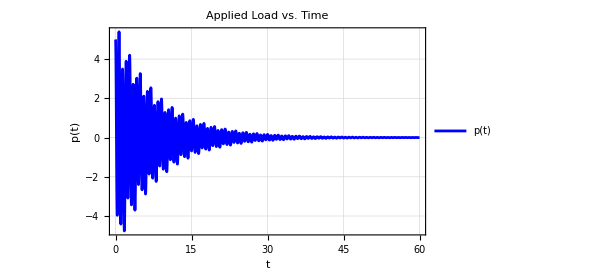

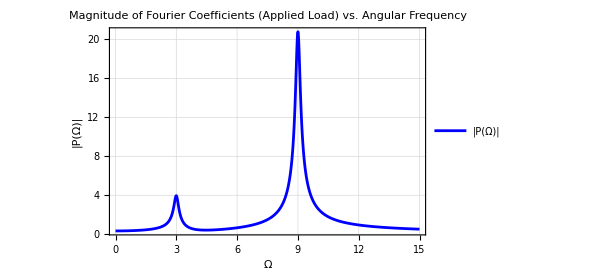

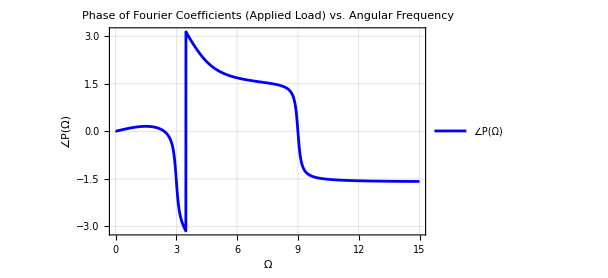

```mathematica
(* Obtain the closed form analytical solution of the Fourier transform of the load. *)
Print[Style["Closed form analytical solution of the Fourier transform of the load:", Bold, FontFamily->"Times", FontSize->14]]
P= Integrate[p*Exp[-I*Ω*t], {t, 0,Infinity}];
P = Chop[FullSimplify[ComplexExpand[P]]]

(* Plot load vs time. *)
Show[Plot[p, {t, 0, 60}, ImageSize->{450, 300}, PlotStyle->{Directive[Blue, AbsoluteThickness[2]]}, PlotLegends->{Style["p(t)", Italic, Bold, FontSize->10, FontFamily->"Times"]},FrameLabel->{Style["t", Italic], Style["p(t)", Italic]}, PlotLabel->"Applied Load vs. Time", GridLines->Automatic, LabelStyle->{RGBColor[0,0,0], Bold, FontSize->10, FontFamily->"Times"}, PlotRange->All, Frame->True]]

(* Plot magnitude of Fourier coefficients vs angular frequency. *)
Show[Plot[Abs[P], {Ω, 0, 15}, ImageSize->{450, 300}, PlotStyle->{Directive[Blue, AbsoluteThickness[2]]},PlotLegends->{Style["|P(Ω)|", Italic, Bold, FontSize->10, FontFamily->"Times"]},FrameLabel->{Style["Ω", Italic], Style["|P(Ω)|", Italic]}, PlotLabel->"Magnitude of Fourier Coefficients (Applied Load) vs. Angular Frequency", GridLines->Automatic, LabelStyle->{RGBColor[0,0,0], Bold, FontSize->10, FontFamily->"Times"}, PlotRange->All, Frame->True]]

(* Plot phase of Fourier coefficients vs angular frequency. *)
Show[Plot[FullSimplify[Arg[P]], {Ω, 0, 15}, ImageSize->{450, 300}, PlotStyle->{Directive[Blue, AbsoluteThickness[2]]},PlotLegends->{Style["∠P(Ω)", Italic, Bold, FontSize->10, FontFamily->"Times"]},FrameLabel->{Style["Ω", Italic], Style["∠P(Ω)", Italic]}, PlotLabel->"Phase of Fourier Coefficients (Applied Load) vs. Angular Frequency", GridLines->Automatic, LabelStyle->{RGBColor[0,0,0], Bold, FontSize->10, FontFamily->"Times"}, PlotRange->All, Frame->True]]
```

The peaks in the Fourier coefficient magnitude plot occur at Ω = 3 rad/s and Ω = 9 rad/s. The 2 angular frequencies corresponding to the 2 peaks are the exact harmonic frequency components involved in the applied load p(t). Also, the ratio of |P(Ω = 9 rad/s)| to |P(Ω = 3 rad/s)| is approximately 5, which is the same as the ratio of amplitude between the 2 harmonic load components involved in the applied load p(t).

## Problem 2

```mathematica
(* Calculate the system properties from structural dynamics for reference. *)
Print[Style[Row[{"Natural frequency ",Subscript[ω,n]," of the system (rad/s):"}], Bold, FontFamily->"Times", FontSize->14]]
ωn = Sqrt[k/m]
Print[Style[Row[{"Damping ratio ζ of the system:"}], Bold, FontFamily->"Times", FontSize->14]]
ζ = c/(2*Sqrt[m*k])
Print[Style[Row[{"Damped frequency ",Subscript[ω,D]," of the system (rad/s):"}], Bold, FontFamily->"Times", FontSize->14]]
ωd = ωn*Sqrt[1-ζ^2]
```

Natural frequency ω_n of the system (rad/s):

√2

Damping ratio ζ of the system:

0.176777

Damped frequency ω_D of the system (rad/s):

1.39194

Impulse response of the system:

-0.718421 ⅇ^(-0.25 t) (1. HeavisideTheta[0] Sin[1.39194 t]-1. HeavisideTheta[t] Sin[1.39194 t])

-0.718421 ⅇ^(-0.25 t) (0.-1. Sin[1.39194 t])

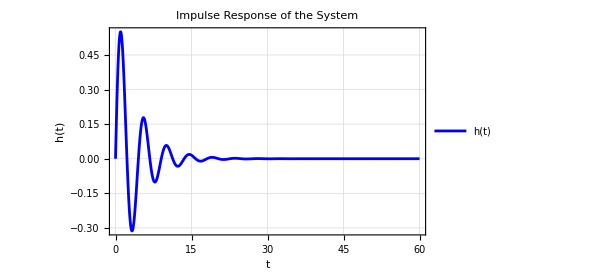

```mathematica
(* Solve the impulse response of the system. *)
Print[Style["Impulse response of the system:", Bold, FontFamily->"Times", FontSize->14]]
temp=DSolve[{m*h''[t]+c*h'[t]+k*h[t]==DiracDelta[t], h[0]==0, h'[0]==0}, h[t], t][[1]];
h = h[t]/.temp
h = h/.{HeavisideTheta[0]->0, HeavisideTheta[t]->1}

(* Plot the impulse response. *)
Show[Plot[h, {t, 0, 60}, ImageSize->{450, 300}, PlotStyle->{Directive[Blue, AbsoluteThickness[2]]}, PlotLegends->{Style["h(t)", Italic, Bold, FontSize->10, FontFamily->"Times"]},FrameLabel->{Style["t", Italic], Style["h(t)", Italic]}, PlotLabel->"Impulse Response of the System", GridLines->Automatic, LabelStyle->{RGBColor[0,0,0], Bold, FontSize->10, FontFamily->"Times"}, PlotRange->All, Frame->True]]
```

The impulse response will not change if the applied load changes. Because the impulse response is the response of the system due to a unit impulse acting on the system. Also, the frequency of the impulse response is the damped frequency of the system which is not relevant to the frequency components of the applied load.

## Problem 3

Closed form analytical solution of the impulse response (FRF):

ConditionalExpression[2./(4.-3.75 Ω^2+1. Ω^4)+(((0.-0.5 ⅈ)-1. Ω) Ω)/(4.-3.75 Ω^2+1. Ω^4), Re[(0.-1. ⅈ) Ω]<0.25&&Re[(0.+1. ⅈ) Ω]>-0.25]

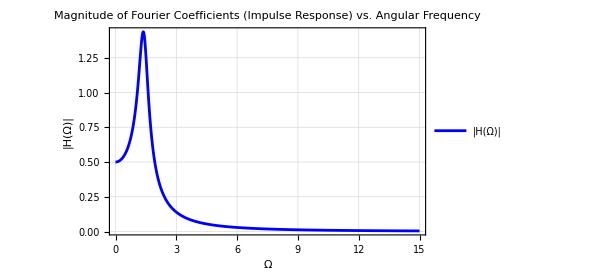

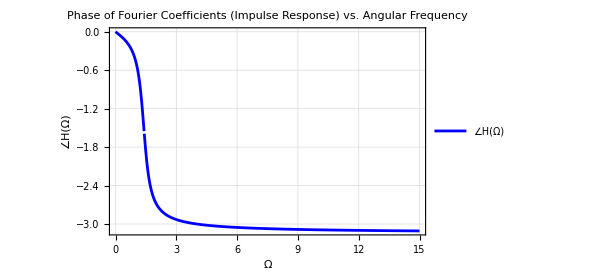

```mathematica
(* Obtain the closed form analytical solution of the Fourier transform of the impulse response. *)
Print[Style["Closed form analytical solution of the impulse response (FRF):", Bold, FontFamily->"Times", FontSize->14]]
H= Integrate[h*Exp[-I*Ω*t], {t, 0,Infinity}];
H = Chop[FullSimplify[ComplexExpand[H]]]

(* Plot magnitude of Fourier coefficients vs angular frequency. *)
Show[Plot[Abs[H], {Ω, 0, 15}, ImageSize->{450, 300}, PlotStyle->{Directive[Blue, AbsoluteThickness[2]]},PlotLegends->{Style["|H(Ω)|", Italic, Bold, FontSize->10, FontFamily->"Times"]},FrameLabel->{Style["Ω", Italic], Style["|H(Ω)|", Italic]}, PlotLabel->"Magnitude of Fourier Coefficients (Impulse Response) vs. Angular Frequency", GridLines->Automatic, LabelStyle->{RGBColor[0,0,0], Bold, FontSize->10, FontFamily->"Times"}, PlotRange->All, Frame->True]]

(* Plot phase of Fourier coefficients vs angular frequency. *)
Show[Plot[FullSimplify[Arg[H]], {Ω, 0, 15}, ImageSize->{450, 300}, PlotStyle->{Directive[Blue, AbsoluteThickness[2]]},PlotLegends->{Style["∠H(Ω)", Italic, Bold, FontSize->10, FontFamily->"Times"]},FrameLabel->{Style["Ω", Italic], Style["∠H(Ω)", Italic]}, PlotLabel->"Phase of Fourier Coefficients (Impulse Response) vs. Angular Frequency", GridLines->Automatic, LabelStyle->{RGBColor[0,0,0], Bold, FontSize->10, FontFamily->"Times"}, PlotRange->All, Frame->True]]
```

In the magnitude plot of the Fourier coefficients for the impulse response, the peak occurs at around Ω = 1.39 rad/s. This is the impulse response frequency of the system, which is the same as the damped natural frequency of the system. There is only one peak in the plot since the impulse response only involves one frequency component which is the system’s damped natural frequency. The impulse response is not relevant to the applied load in the system.

## Problem 4

Response of the system under the applied load:

ⅇ^(-0.25 t) (0.078722 Cos[1.39194 t]+0.297454 Sin[1.39194 t])+ⅇ^(-0.12 t) (0.0012094 Cos[3. t]-0.0167321 Cos[3. t]-0.0631992 Cos[9. t]+0.0408585 Sin[3. t]-0.181073 Sin[3. t]+0.0018709 Sin[9. t])

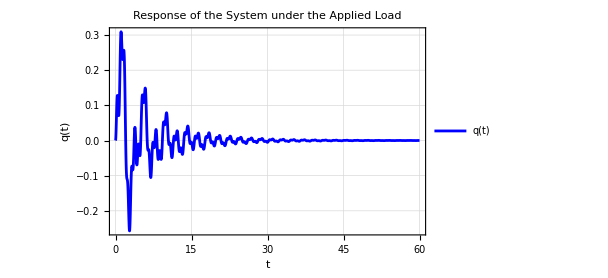

```mathematica
(* Solve the response of the system under the applied load. *)
Print[Style["Response of the system under the applied load:", Bold, FontFamily->"Times", FontSize->14]]
temp= DSolve[{m*q''[t]+c*q'[t]+k*q[t]==p, q[0]==0, q'[0]==0}, q[t], t][[1]];
temp = Chop[FullSimplify[ComplexExpand[Re[temp]]]];
q=q[t]/.temp

(* Plot the response of the system under the applied load. *)
Show[Plot[q, {t, 0, 60}, ImageSize->{450, 300}, PlotStyle->{Directive[Blue, AbsoluteThickness[2]]}, PlotLegends->{Style["q(t)", Italic, Bold, FontSize->10, FontFamily->"Times"]},FrameLabel->{Style["t", Italic], Style["q(t)", Italic]}, PlotLabel->"Response of the System under the Applied Load", GridLines->Automatic, LabelStyle->{RGBColor[0,0,0], Bold, FontSize->10, FontFamily->"Times"}, PlotRange->All, Frame->True]]
```

In the solution, the terms with frequency component of 1.39 rad/s (damped natural frequency of the system) are corresponding to the transient response. The terms with frequency components of 3 rad/s and 9 rad/s (harmonic frequencies of the applied load) are corresponding to the steady state response.

## Problem 5

Closed form analytical solution of the system response under applied load:

ConditionalExpression[(2.9488×10^7+Ω ((0.-2.79244×10^6 ⅈ)+Ω (-2.41665×10^7+Ω ((1.39268×10^-9-1.89046×10^6 ⅈ)+Ω ((6.07026×10^6+1.00833×10^-10 ⅈ)+Ω ((1.74623×10^-10+1.19309×10^6 ⅈ)+Ω (-641415.+Ω ((0.-220519. ⅈ)+Ω (27750.1+Ω ((0.+17722.8 ⅈ)+Ω (-306.754+Ω ((0.-592.72 ⅈ)+(-0.1+(0.+5. ⅈ) Ω) Ω))))))))))))/(1.73353×10^8+Ω^2 (-2.43474×10^8+Ω (1.19747×10^-8+Ω (1.33898×10^8+Ω (-8.78353×10^-9+Ω (-3.52563×10^7+Ω (1.46943×10^-9+Ω (4.908×10^6+Ω^2 (-366513.+Ω^2 (13616.6+Ω (-201.664 Ω+1. Ω^3))))))))))), Re[(0.-1. ⅈ) Ω]<0.12&&Re[(0.+1. ⅈ) Ω]≥-0.12]

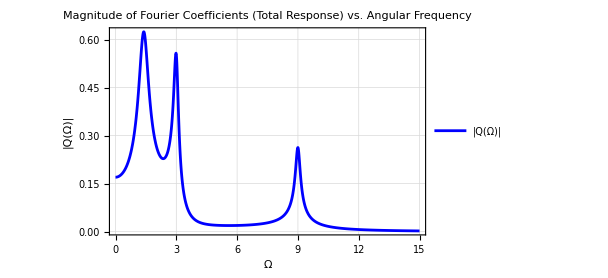

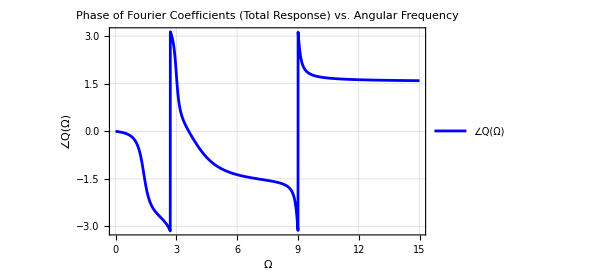

```mathematica
(* Obtain the closed form analytical solution of the Fourier transform of the system response under applied load. *)
Print[Style["Closed form analytical solution of the system response under applied load:", Bold, FontFamily->"Times", FontSize->14]]
Q= Integrate[q*Exp[-I*Ω*t], {t, 0,Infinity}];
Q = Chop[FullSimplify[ComplexExpand[Q]]]

(* Plot magnitude of Fourier coefficients vs angular frequency. *)
Show[Plot[Abs[Q], {Ω, 0, 15}, ImageSize->{450, 300}, PlotStyle->{Directive[Blue, AbsoluteThickness[2]]},PlotLegends->{Style["|Q(Ω)|", Italic, Bold, FontSize->10, FontFamily->"Times"]},FrameLabel->{Style["Ω", Italic], Style["|Q(Ω)|", Italic]}, PlotLabel->"Magnitude of Fourier Coefficients (Total Response) vs. Angular Frequency", GridLines->Automatic, LabelStyle->{RGBColor[0,0,0], Bold, FontSize->10, FontFamily->"Times"}, PlotRange->All, Frame->True]]

(* Plot phase of Fourier coefficients vs angular frequency. *)
Show[Plot[FullSimplify[Arg[Q]], {Ω, 0, 15}, ImageSize->{450, 300}, PlotStyle->{Directive[Blue, AbsoluteThickness[2]]},PlotLegends->{Style["∠Q(Ω)", Italic, Bold, FontSize->10, FontFamily->"Times"]},FrameLabel->{Style["Ω", Italic], Style["∠Q(Ω)", Italic]}, PlotLabel->"Phase of Fourier Coefficients (Total Response) vs. Angular Frequency", GridLines->Automatic, LabelStyle->{RGBColor[0,0,0], Bold, FontSize->10, FontFamily->"Times"}, PlotRange->All, Frame->True]]
```

The peaks in the Fourier coefficient magnitude plot of the total system response under applied load occur at Ω = 1.39 rad/s, Ω = 3 rad/s and Ω = 9 rad/s. The 3 peaks are corresponding to the 3 frequency components involved in the total system response. Ω = 1.39 rad/s is transient response frequency, which is the same as the damped natural frequency of the system. Ω = 3 rad/s and Ω = 9 rad/s are the steady state frequencies, which are the same as the harmonic frequencies of the applied load. The values at the 3 peaks represent the amplitude of the total system response for the 3 frequency components. The response with frequency Ω = 1.39 rad/s has the largest amplitude and the response with frequency Ω = 9 rad/s has the least amplitude.

## Problem 6

Cross power spectral density S_xy:

ConditionalExpression[((181443.+Ω ((0.+28178.6 ⅈ)+Ω (-24895.+Ω ((0.-7566.72 ⅈ)+Ω (550.783+Ω ((0.+494.064 ⅈ)+(-2.4-(0.+5. ⅈ) Ω) Ω)))))) (2.9488×10^7+Conjugate[Ω] ((0.+2.79244×10^6 ⅈ)+Conjugate[Ω] (-2.41665×10^7+Conjugate[Ω] ((1.39268×10^-9+1.89046×10^6 ⅈ)+Conjugate[Ω] ((6.07026×10^6-1.00833×10^-10 ⅈ)+Conjugate[Ω] ((1.74623×10^-10-1.19309×10^6 ⅈ)+Conjugate[Ω] (-641415.+Conjugate[Ω] ((0.+220519. ⅈ)+Conjugate[Ω] (27750.1+Conjugate[Ω] ((0.-17722.8 ⅈ)+Conjugate[Ω] (-306.754+Conjugate[Ω] ((0.+592.72 ⅈ)+(-0.1-(0.+5. ⅈ) Conjugate[Ω]) Conjugate[Ω])))))))))))))/((533333.+Ω^2 (-131113.+Ω^2 (9555.41+Ω^2 (-179.942+1. Ω^2)))) (1.73353×10^8+Conjugate[Ω]^2 (-2.43474×10^8+Conjugate[Ω] (1.19747×10^-8+Conjugate[Ω] (1.33898×10^8+Conjugate[Ω] (-8.78353×10^-9+Conjugate[Ω] (-3.52563×10^7+Conjugate[Ω] (1.46943×10^-9+Conjugate[Ω] (4.908×10^6+Conjugate[Ω]^2 (-366513.+Conjugate[Ω]^2 (13616.6+Conjugate[Ω] (-201.664 Conjugate[Ω]+1. Conjugate[Ω]^3)))))))))))), ]

Cross power spectral density S_yx:

ConditionalExpression[((2.9488×10^7+Ω ((0.-2.79244×10^6 ⅈ)+Ω (-2.41665×10^7+Ω ((1.39268×10^-9-1.89046×10^6 ⅈ)+Ω ((6.07026×10^6+1.00833×10^-10 ⅈ)+Ω ((1.74623×10^-10+1.19309×10^6 ⅈ)+Ω (-641415.+Ω ((0.-220519. ⅈ)+Ω (27750.1+Ω ((0.+17722.8 ⅈ)+Ω (-306.754+Ω ((0.-592.72 ⅈ)+(-0.1+(0.+5. ⅈ) Ω) Ω)))))))))))) (181443.+Conjugate[Ω] ((0.-28178.6 ⅈ)+Conjugate[Ω] (-24895.+Conjugate[Ω] ((0.+7566.72 ⅈ)+Conjugate[Ω] (550.783+Conjugate[Ω] ((0.-494.064 ⅈ)+(-2.4+(0.+5. ⅈ) Conjugate[Ω]) Conjugate[Ω])))))))/((1.73353×10^8+Ω^2 (-2.43474×10^8+Ω (1.19747×10^-8+Ω (1.33898×10^8+Ω (-8.78353×10^-9+Ω (-3.52563×10^7+Ω (1.46943×10^-9+Ω (4.908×10^6+Ω^2 (-366513.+Ω^2 (13616.6+Ω (-201.664 Ω+1. Ω^3))))))))))) (533333.+Conjugate[Ω]^2 (-131113.+Conjugate[Ω]^2 (9555.41+Conjugate[Ω]^2 (-179.942+1. Conjugate[Ω]^2))))), ]

Auto power spectral density S_xx:

ConditionalExpression[((181443.+Ω ((0.+28178.6 ⅈ)+Ω (-24895.+Ω ((0.-7566.72 ⅈ)+Ω (550.783+Ω ((0.+494.064 ⅈ)+(-2.4-(0.+5. ⅈ) Ω) Ω)))))) (181443.+Conjugate[Ω] ((0.-28178.6 ⅈ)+Conjugate[Ω] (-24895.+Conjugate[Ω] ((0.+7566.72 ⅈ)+Conjugate[Ω] (550.783+Conjugate[Ω] ((0.-494.064 ⅈ)+(-2.4+(0.+5. ⅈ) Conjugate[Ω]) Conjugate[Ω])))))))/((533333.+Ω^2 (-131113.+Ω^2 (9555.41+Ω^2 (-179.942+1. Ω^2)))) (533333.+Conjugate[Ω]^2 (-131113.+Conjugate[Ω]^2 (9555.41+Conjugate[Ω]^2 (-179.942+1. Conjugate[Ω]^2))))), Re[(0.-1. ⅈ) Ω]<0.12&&Re[(0.+1. ⅈ) Ω]>-0.12]

Auto power spectral density S_yy:

ConditionalExpression[((2.9488×10^7+Ω ((0.-2.79244×10^6 ⅈ)+Ω (-2.41665×10^7+Ω ((1.39268×10^-9-1.89046×10^6 ⅈ)+Ω ((6.07026×10^6+1.00833×10^-10 ⅈ)+Ω ((1.74623×10^-10+1.19309×10^6 ⅈ)+Ω (-641415.+Ω ((0.-220519. ⅈ)+Ω (27750.1+Ω ((0.+17722.8 ⅈ)+Ω (-306.754+Ω ((0.-592.72 ⅈ)+(-0.1+(0.+5. ⅈ) Ω) Ω)))))))))))) (2.9488×10^7+Conjugate[Ω] ((0.+2.79244×10^6 ⅈ)+Conjugate[Ω] (-2.41665×10^7+Conjugate[Ω] ((1.39268×10^-9+1.89046×10^6 ⅈ)+Conjugate[Ω] ((6.07026×10^6-1.00833×10^-10 ⅈ)+Conjugate[Ω] ((1.74623×10^-10-1.19309×10^6 ⅈ)+Conjugate[Ω] (-641415.+Conjugate[Ω] ((0.+220519. ⅈ)+Conjugate[Ω] (27750.1+Conjugate[Ω] ((0.-17722.8 ⅈ)+Conjugate[Ω] (-306.754+Conjugate[Ω] ((0.+592.72 ⅈ)+(-0.1-(0.+5. ⅈ) Conjugate[Ω]) Conjugate[Ω])))))))))))))/((1.73353×10^8+Ω^2 (-2.43474×10^8+Ω (1.19747×10^-8+Ω (1.33898×10^8+Ω (-8.78353×10^-9+Ω (-3.52563×10^7+Ω (1.46943×10^-9+Ω (4.908×10^6+Ω^2 (-366513.+Ω^2 (13616.6+Ω (-201.664 Ω+1. Ω^3))))))))))) (1.73353×10^8+Conjugate[Ω]^2 (-2.43474×10^8+Conjugate[Ω] (1.19747×10^-8+Conjugate[Ω] (1.33898×10^8+Conjugate[Ω] (-8.78353×10^-9+Conjugate[Ω] (-3.52563×10^7+Conjugate[Ω] (1.46943×10^-9+Conjugate[Ω] (4.908×10^6+Conjugate[Ω]^2 (-366513.+Conjugate[Ω]^2 (13616.6+Conjugate[Ω] (-201.664 Conjugate[Ω]+1. Conjugate[Ω]^3)))))))))))), Re[(0.-1. ⅈ) Ω]<0.12&&Re[(0.+1. ⅈ) Ω]≥-0.12]

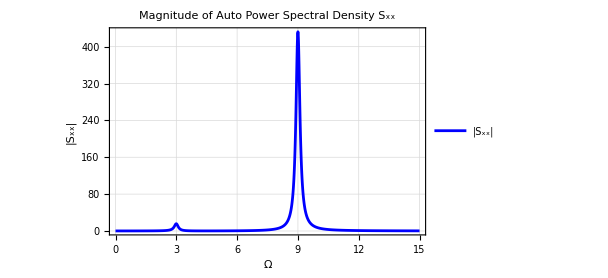

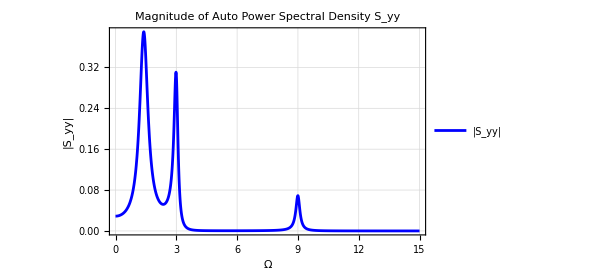

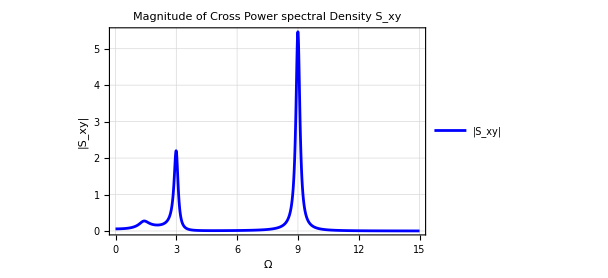

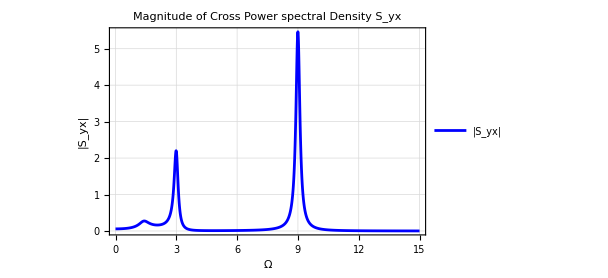

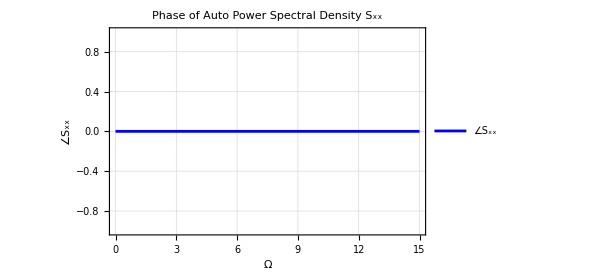

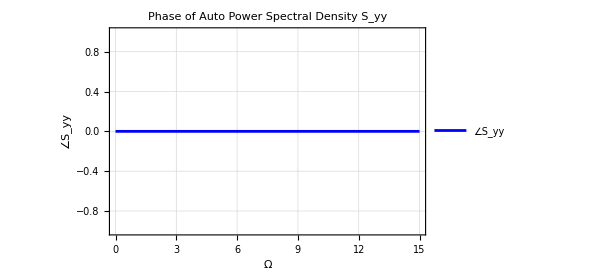

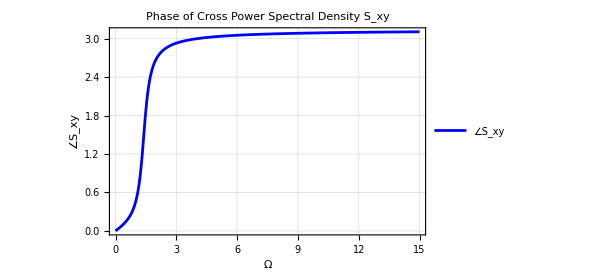

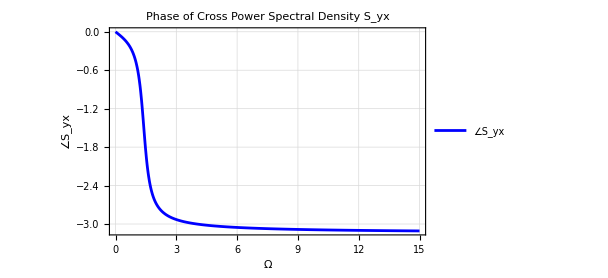

```mathematica
(* Calculate the cross power spectral density Sxy and Syx. *)
Print[Style[Row[{"Cross power spectral density ",Subscript[S,xy],":"}], Bold, FontFamily->"Times", FontSize->14]]
Sxy = P * Conjugate[Q]

Print[Style[Row[{"Cross power spectral density ",Subscript[S,yx],":"}], Bold, FontFamily->"Times", FontSize->14]]
Syx = Q * Conjugate[P]

(* Calculate the auto power spectral density Sxx and Syy. *)
Print[Style[Row[{"Auto power spectral density ",Subscript[S,xx],":"}], Bold, FontFamily->"Times", FontSize->14]]
Sxx = P * Conjugate[P]

Print[Style[Row[{"Auto power spectral density ",Subscript[S,yy],":"}], Bold, FontFamily->"Times", FontSize->14]]
Syy = Q * Conjugate[Q]

(* Plot the magnitude of auto power spectral density Sxx. *)
Show[Plot[Abs[Sxx], {Ω, 0, 15}, ImageSize->{450, 300}, PlotStyle->{Directive[Blue, AbsoluteThickness[2]]},PlotLegends->{Style[Row[{"|",Subscript[S,xx],"|"}], Italic, Bold, FontSize->10, FontFamily->"Times"]},FrameLabel->{Style["Ω", Italic], Style[Row[{"|",Subscript[S,xx],"|"}], Italic]}, PlotLabel->Row[{"Magnitude of Auto Power Spectral Density ",Subscript[S,xx]}], GridLines->Automatic, LabelStyle->{RGBColor[0,0,0], Bold, FontSize->10, FontFamily->"Times"}, PlotRange->All, Frame->True]]

(* Plot the magnitude of auto power spectral density Syy. *)
Show[Plot[Abs[Syy], {Ω, 0, 15}, ImageSize->{450, 300}, PlotStyle->{Directive[Blue, AbsoluteThickness[2]]},PlotLegends->{Style[Row[{"|",Subscript[S,yy],"|"}], Italic, Bold, FontSize->10, FontFamily->"Times"]},FrameLabel->{Style["Ω", Italic], Style[Row[{"|",Subscript[S,yy],"|"}], Italic]}, PlotLabel->Row[{"Magnitude of Auto Power Spectral Density ",Subscript[S,yy]}], GridLines->Automatic, LabelStyle->{RGBColor[0,0,0], Bold, FontSize->10, FontFamily->"Times"}, PlotRange->All, Frame->True]]

(* Plot the magnitude of cross power spectral density Sxy. *)
Show[Plot[Abs[Sxy], {Ω, 0, 15}, ImageSize->{450, 300}, PlotStyle->{Directive[Blue, AbsoluteThickness[2]]},PlotLegends->{Style[Row[{"|",Subscript[S,xy],"|"}], Italic, Bold, FontSize->10, FontFamily->"Times"]},FrameLabel->{Style["Ω", Italic], Style[Row[{"|",Subscript[S,xy],"|"}], Italic]}, PlotLabel->Row[{"Magnitude of Cross Power spectral Density ",Subscript[S,xy]}], GridLines->Automatic, LabelStyle->{RGBColor[0,0,0], Bold, FontSize->10, FontFamily->"Times"}, PlotRange->All, Frame->True]]

(* Plot the magnitude of cross power spectral density Syx. *)
Show[Plot[Abs[Syx], {Ω, 0, 15}, ImageSize->{450, 300}, PlotStyle->{Directive[Blue, AbsoluteThickness[2]]},PlotLegends->{Style[Row[{"|",Subscript[S,yx],"|"}], Italic, Bold, FontSize->10, FontFamily->"Times"]},FrameLabel->{Style["Ω", Italic], Style[Row[{"|",Subscript[S,yx],"|"}], Italic]}, PlotLabel->Row[{"Magnitude of Cross Power spectral Density ",Subscript[S,yx]}], GridLines->Automatic, LabelStyle->{RGBColor[0,0,0], Bold, FontSize->10, FontFamily->"Times"}, PlotRange->All, Frame->True]]

(* Plot the phase of auto power spectral density Sxx. *)
Show[Plot[FullSimplify[Arg[Sxx]], {Ω, 0, 15}, ImageSize->{450, 300}, PlotStyle->{Directive[Blue, AbsoluteThickness[2]]},PlotLegends->{Style[Row[{"∠",Subscript[S,xx]}], Italic, Bold, FontSize->10, FontFamily->"Times"]},FrameLabel->{Style["Ω", Italic], Style[Row[{"∠",Subscript[S,xx]}], Italic]}, PlotLabel->Row[{"Phase of Auto Power Spectral Density ",Subscript[S,xx]}], GridLines->Automatic, LabelStyle->{RGBColor[0,0,0], Bold, FontSize->10, FontFamily->"Times"}, PlotRange->All, Frame->True]]

(* Plot the phase of auto power spectral density Syy. *)
Show[Plot[FullSimplify[Arg[Syy]], {Ω, 0, 15}, ImageSize->{450, 300}, PlotStyle->{Directive[Blue, AbsoluteThickness[2]]},PlotLegends->{Style[Row[{"∠",Subscript[S,yy]}], Italic, Bold, FontSize->10, FontFamily->"Times"]},FrameLabel->{Style["Ω", Italic], Style[Row[{"∠",Subscript[S,yy]}], Italic]}, PlotLabel->Row[{"Phase of Auto Power Spectral Density ",Subscript[S,yy]}], GridLines->Automatic, LabelStyle->{RGBColor[0,0,0], Bold, FontSize->10, FontFamily->"Times"}, PlotRange->All, Frame->True]]

(* Plot the phase of cross power spectral density Sxy. *)
Show[Plot[FullSimplify[Arg[Sxy]], {Ω, 0, 15}, ImageSize->{450, 300}, PlotStyle->{Directive[Blue, AbsoluteThickness[2]]},PlotLegends->{Style[Row[{"∠",Subscript[S,xy]}], Italic, Bold, FontSize->10, FontFamily->"Times"]},FrameLabel->{Style["Ω", Italic], Style[Row[{"∠",Subscript[S,xy]}], Italic]}, PlotLabel->Row[{"Phase of Cross Power Spectral Density ",Subscript[S,xy]}], GridLines->Automatic, LabelStyle->{RGBColor[0,0,0], Bold, FontSize->10, FontFamily->"Times"}, PlotRange->All, Frame->True]]

(* Plot the phase of cross power spectral density Syx. *)
Show[Plot[FullSimplify[Arg[Syx]], {Ω, 0, 15}, ImageSize->{450, 300}, PlotStyle->{Directive[Blue, AbsoluteThickness[2]]},PlotLegends->{Style[Row[{"∠",Subscript[S,yx]}], Italic, Bold, FontSize->10, FontFamily->"Times"]},FrameLabel->{Style["Ω", Italic], Style[Row[{"∠",Subscript[S,yx]}], Italic]}, PlotLabel->Row[{"Phase of Cross Power Spectral Density ",Subscript[S,yx]}], GridLines->Automatic, LabelStyle->{RGBColor[0,0,0], Bold, FontSize->10, FontFamily->"Times"}, PlotRange->All, Frame->True]]
```

Discussions:

(1) In the magnitude plot of auto PSD for input |S_xx|, the 2 peaks occur at Ω = 3 rad/s and Ω = 9 rad/s. These 2 angular frequencies corresponding to the 2 peaks are the exact harmonic frequency components involved in the applied load p(t). Also, the ratio of |S_xx(Ω = 9 rad/s)| to |S_xx(Ω = 3 rad/s)| is approximately 25, which is the same as the square of the ratio of amplitude between the 2 harmonic load components involved in the applied load p(t).

(2) In the magnitude plot of auto PSD for output |S_yy|, the 3 peaks occur at Ω = 1.39 rad/s, Ω = 3 rad/s and Ω = 9 rad/s. These 3 angular frequencies corresponding to the 3 peaks are the exact harmonic frequency components involved in the total system response. Ω = 1.39 rad/s is transient response frequency, which is the same as the damped natural frequency of the system. Ω = 3 rad/s and Ω = 9 rad/s are the steady state frequencies, which are the same as the harmonic frequencies of the applied load. The values at the 3 peaks represent the amplitude of the total system response for the 3 frequency components. The response with frequency Ω = 1.39 rad/s has the largest amplitude and the response with frequency Ω = 9 rad/s has the least amplitude.

(3) The phase plot of auto PSD ∠S_xx and ∠S_yy are both zero values because there is no phase difference between a signal and itself.

(4)  For the cross PSD S_xy and S_yx, they are complex conjugate of each other. So the 2 cross PSD have the same magnitude plot and the negative phase plot. In the magnitude plots, the 3 peaks occur at Ω = 1.39 rad/s, Ω = 3 rad/s and Ω = 9 rad/s. These 3 angular frequencies corresponding to the 3 peaks are the exact harmonic frequency components involved in the total system response.

## Problem 7

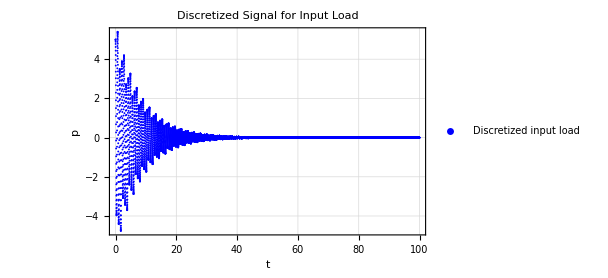

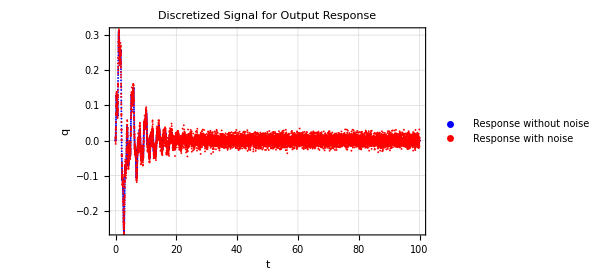

```mathematica
(* Sample the input and output at frequency of 100 Hz. *)
fs = 100; (* Sampling frequency in Hz. *)
timestamps = Range[0, 100, 1/fs];(* Sampling timestamps. *)

(* Discretize the input and output signal at the sampling timestamps. *)
pSeq= p/. t->#&/@timestamps;
qSeq = q/. t->#&/@timestamps;

(* Add zero-mean Gaussian noise to the output sequence q[n]. *)
GaussianNoise = RandomVariate[NormalDistribution[0, Max[qSeq]/30], Length[qSeq]];
qSeqNoisy = qSeq + GaussianNoise;

(* Plot the discretized input and output signal. *)
pSeqList = Transpose[{timestamps, pSeq}];
qSeqList = Transpose[{timestamps, qSeq}];
qSeqNoisyList = Transpose[{timestamps, qSeqNoisy}];

Show[ListPlot[pSeqList, ImageSize->{450, 300}, PlotStyle->{Directive[Blue, PointSize[0.003]]},PlotLegends->{Style["Discretized input load", Bold, FontSize->10, FontFamily->"Times"]},FrameLabel->{Style["t", Italic], Style["p", Italic]}, PlotLabel->"Discretized Signal for Input Load", GridLines->Automatic, LabelStyle->{RGBColor[0,0,0], Bold, FontSize->10, FontFamily->"Times"}, PlotRange->All, Frame->True]]

Show[ListPlot[qSeqList, ImageSize->{450, 300}, PlotStyle->{Directive[Blue, PointSize[0.003]]},PlotLegends->{Style["Response without noise", Bold, FontSize->10, FontFamily->"Times"]},FrameLabel->{Style["t", Italic], Style["q", Italic]}, PlotLabel->"Discretized Signal for Output Response", GridLines->Automatic, LabelStyle->{RGBColor[0,0,0], Bold, FontSize->10, FontFamily->"Times"}, PlotRange->All, Frame->True],
ListPlot[qSeqNoisyList, ImageSize->{450, 300}, PlotStyle->{Directive[Red, PointSize[0.003]]},PlotLegends->{Style["Response with noise", Bold, FontSize->10, FontFamily->"Times"]},FrameLabel->{Style["t", Italic], Style["q", Italic]}, PlotLabel->"Discretized Signal for Output Response", GridLines->Automatic, LabelStyle->{RGBColor[0,0,0], Bold, FontSize->10, FontFamily->"Times"}, PlotRange->All, Frame->True]]
```

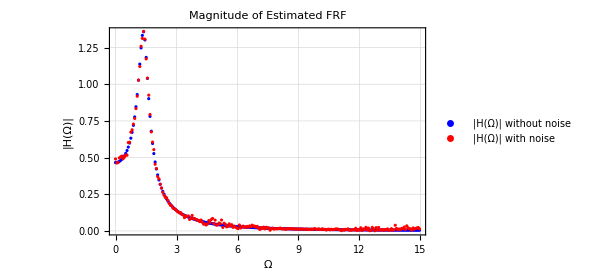

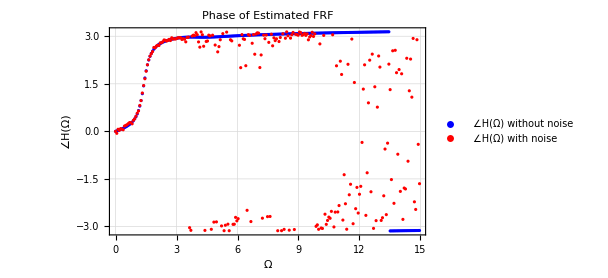

```mathematica
(* Obtain the DFT of the input and output sequence using FFT algorithm. *)
Npoints = Length[pSeq]; (* Number of data points in each sequence. *)
PSeq = Fourier[pSeq];
QSeq= Fourier[qSeq];
QSeqNoisy = Fourier[qSeqNoisy];

(* Limit the angular frequency between 0 and 15 rad/s. *)
Frequency = Range[0, 2Pi(1-1/Npoints), 2Pi/Npoints]*fs;
Frequency = DeleteCases[Frequency, x_/; x>15];

PSeq= Take[PSeq, Length[Frequency]];
QSeq= Take[QSeq, Length[Frequency]];
QSeqNoisy = Take[QSeqNoisy, Length[Frequency]];

(* Obtain the DFT of impulse response (FRF sequence). *)
HSeq = QSeq / PSeq; (* Estimation from the noise-free data. *)
HSeqListMagnitude =  Transpose[{Frequency, Abs[HSeq]}];
HSeqListPhase=  Transpose[{Frequency, Arg[HSeq]}];

HSeqNoisy = QSeqNoisy / PSeq; (* Estimation from the noisy data. *)
HSeqNoisyListMagnitude =  Transpose[{Frequency, Abs[HSeqNoisy]}];
HSeqNoisyListPhase=  Transpose[{Frequency, Arg[HSeqNoisy]}];

Show[ListPlot[HSeqListMagnitude, ImageSize->{450, 300}, PlotStyle->{Directive[Blue, PointSize[0.005]]},PlotLegends->{Style["|H(Ω)| without noise", Bold, FontSize->10, FontFamily->"Times"]},FrameLabel->{Style["Ω", Italic], Style["|H(Ω)|", Italic]}, PlotLabel->"Magnitude of Estimated FRF", GridLines->Automatic, LabelStyle->{RGBColor[0,0,0], Bold, FontSize->10, FontFamily->"Times"}, PlotRange->All, Frame->True],
ListPlot[HSeqNoisyListMagnitude, ImageSize->{450, 300}, PlotStyle->{Directive[Red, PointSize[0.005]]},PlotLegends->{Style["|H(Ω)| with noise", Bold, FontSize->10, FontFamily->"Times"]},FrameLabel->{Style["Ω", Italic], Style["|H(Ω)|", Italic]}, PlotLabel->"Magnitude of Estimated FRF", GridLines->Automatic, LabelStyle->{RGBColor[0,0,0], Bold, FontSize->10, FontFamily->"Times"}, PlotRange->All, Frame->True]]

Show[ListPlot[HSeqListPhase, ImageSize->{450, 300}, PlotStyle->{Directive[Blue, PointSize[0.005]]},PlotLegends->{Style["∠H(Ω) without noise", Bold, FontSize->10, FontFamily->"Times"]},FrameLabel->{Style["Ω", Italic], Style["∠H(Ω)", Italic]}, PlotLabel->"Phase of Estimated FRF", GridLines->Automatic, LabelStyle->{RGBColor[0,0,0], Bold, FontSize->10, FontFamily->"Times"}, PlotRange->All, Frame->True],
ListPlot[HSeqNoisyListPhase, ImageSize->{450, 300}, PlotStyle->{Directive[Red, PointSize[0.005]]},PlotLegends->{Style["∠H(Ω) with noise", Bold, FontSize->10, FontFamily->"Times"]},FrameLabel->{Style["Ω", Italic], Style["∠H(Ω)", Italic]}, PlotLabel->"Phase of Estimated FRF", GridLines->Automatic, LabelStyle->{RGBColor[0,0,0], Bold, FontSize->10, FontFamily->"Times"}, PlotRange->All, Frame->True]]
```

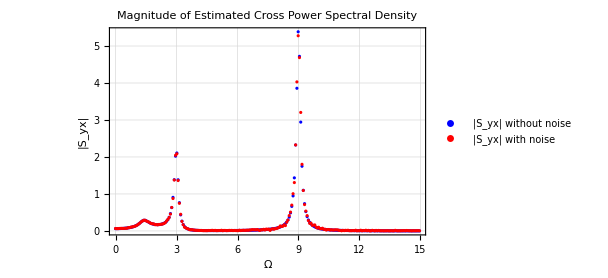

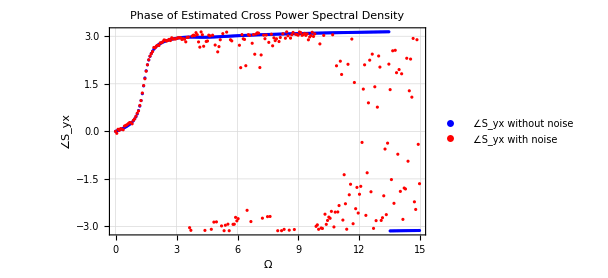

```mathematica
(* Obtain the cross power spectral density sequence Syx. *)
SyxSeq = QSeq * Conjugate[PSeq];
SyxSeqListMagnitude =  Transpose[{Frequency, Abs[SyxSeq]}];
SyxSeqListPhase=  Transpose[{Frequency, Arg[SyxSeq]}];

SyxSeqNoisy = QSeqNoisy * Conjugate[PSeq];
SyxSeqNoisyListMagnitude =  Transpose[{Frequency, Abs[SyxSeqNoisy]}];
SyxSeqNoisyListPhase=  Transpose[{Frequency, Arg[SyxSeqNoisy]}];

Show[ListPlot[SyxSeqListMagnitude, ImageSize->{450, 300}, PlotStyle->{Directive[Blue, PointSize[0.005]]},PlotLegends->{Style[Row[{"|",Subscript[S,yx],"| without noise"}], Bold, FontSize->10, FontFamily->"Times"]},FrameLabel->{Style["Ω", Italic], Style[Row[{"|",Subscript[S,yx],"|"}], Italic]}, PlotLabel->"Magnitude of Estimated Cross Power Spectral Density", GridLines->Automatic, LabelStyle->{RGBColor[0,0,0], Bold, FontSize->10, FontFamily->"Times"}, PlotRange->All, Frame->True],
ListPlot[SyxSeqNoisyListMagnitude, ImageSize->{450, 300}, PlotStyle->{Directive[Red, PointSize[0.005]]},PlotLegends->{Style[Row[{"|",Subscript[S,yx],"| with noise"}], Bold, FontSize->10, FontFamily->"Times"]},FrameLabel->{Style["Ω", Italic], Style[Row[{"|",Subscript[S,yx],"|"}], Italic]}, PlotLabel->"Magnitude of Estimated Cross Power Spectral Density", GridLines->Automatic, LabelStyle->{RGBColor[0,0,0], Bold, FontSize->10, FontFamily->"Times"}, PlotRange->All, Frame->True]]

Show[ListPlot[SyxSeqListPhase, ImageSize->{450, 300}, PlotStyle->{Directive[Blue, PointSize[0.005]]},PlotLegends->{Style[Row[{"∠",Subscript[S,yx]," without noise"}], Bold, FontSize->10, FontFamily->"Times"]},FrameLabel->{Style["Ω", Italic], Style[Row[{"∠",Subscript[S,yx]}], Italic]}, PlotLabel->"Phase of Estimated Cross Power Spectral Density", GridLines->Automatic, LabelStyle->{RGBColor[0,0,0], Bold, FontSize->10, FontFamily->"Times"}, PlotRange->All, Frame->True],
ListPlot[SyxSeqNoisyListPhase, ImageSize->{450, 300}, PlotStyle->{Directive[Red, PointSize[0.005]]},PlotLegends->{Style[Row[{"∠",Subscript[S,yx]," with noise"}], Bold, FontSize->10, FontFamily->"Times"]},FrameLabel->{Style["Ω", Italic], Style[Row[{"∠",Subscript[S,yx]}], Italic]}, PlotLabel->"Phase of Estimated Cross Power Spectral Density", GridLines->Automatic, LabelStyle->{RGBColor[0,0,0], Bold, FontSize->10, FontFamily->"Times"}, PlotRange->All, Frame->True]]
```

Discussions:

(1) For the discretized output response, the Gaussian noise causes some difference between the noisy signal and the original noise-free signal, especially for the part where the amplitude is small. This is because the noise-induced amplitude is zero-mean and with constant deviation. The signal-to-noise ratio in the low amplitude part becomes smaller.

(2) Compared to the estimation of magnitude, the noise has more impact on the estimation of phase. The phase is more sensitive to the measurement noise.

(3) For the phase estimation of both FRF and PSD, large difference between the noisy signal and the noise-free signal occurs in the region of Ω = 4 rad/s - 8 rad/s and Ω > 10 rad/s. In this regions, the magnitude of the cross power spectral density is small, which leads to a small signal-to-noise ratio. So the effect of the noise becomes larger.

## Problem 8

```mathematica
ClearAll["Global'*"]

(* Define the material and geometry properties. *)
e = 70000000000; (* Elastic modulus in Pa. *)
A = 0.0016; (* Cross sectional area in m^2. *)
L = 20; (* Element length in m. *)
ρ = 2700; (* Density of the material in kg/m^3. *)

(* Define the stiffness, mass and damping. *)
Ksystem={{(2 A e)/L,0,-(A e)/L,0,0,0,0,0,0,0,0,0},{0,(A e)/L,0,0,0,0,0,-(A e)/L,0,0,0,0},{-(A e)/L,0,(2 A e)/L+(A e)/(√2 L),0,0,0,-(A e)/(2 √2 L),(A e)/(2 √2 L),0,0,-(A e)/(2 √2 L),-(A e)/(2 √2 L)},{0,0,0,(A e)/L+(A e)/(√2 L),0,0,(A e)/(2 √2 L),-(A e)/(2 √2 L),0,-(A e)/L,-(A e)/(2 √2 L),-(A e)/(2 √2 L)},{0,0,0,0,(A e)/L,0,-(A e)/L,0,0,0,0,0},{0,0,0,0,0,(A e)/L,0,0,0,0,0,0},{0,0,-(A e)/(2 √2 L),(A e)/(2 √2 L),-(A e)/L,0,(2 A e)/L+(A e)/(√2 L),0,-(A e)/L,0,0,0},{0,-(A e)/L,(A e)/(2 √2 L),-(A e)/(2 √2 L),0,0,0,(A e)/L+(A e)/(√2 L),0,0,0,0},{0,0,0,0,0,0,-(A e)/L,0,(2 A e)/L,0,-(A e)/L,0},{0,0,0,-(A e)/L,0,0,0,0,0,(A e)/L,0,0},{0,0,-(A e)/(2 √2 L),-(A e)/(2 √2 L),0,0,0,0,-(A e)/L,0,(A e)/L+(A e)/(2 √2 L),(A e)/(2 √2 L)},{0,0,-(A e)/(2 √2 L),-(A e)/(2 √2 L),0,0,0,0,0,0,(A e)/(2 √2 L),(A e)/L+(A e)/(2 √2 L)}};

Msystem={{(2 A L ρ)/3,0,(A L ρ)/6,0,0,0,0,0,0,0,0,0},{0,(A L ρ)/3,0,0,0,0,0,(A L ρ)/6,0,0,0,0},{(A L ρ)/6,0,(2 A L ρ)/3+1/3 √2 A L ρ,0,0,0,(A L ρ)/(6 √2),-(A L ρ)/(6 √2),0,0,(A L ρ)/(6 √2),(A L ρ)/(6 √2)},{0,0,0,(A L ρ)/3+1/3 √2 A L ρ,0,0,-(A L ρ)/(6 √2),(A L ρ)/(6 √2),0,(A L ρ)/6,(A L ρ)/(6 √2),(A L ρ)/(6 √2)},{0,0,0,0,(A L ρ)/3,0,(A L ρ)/6,0,0,0,0,0},{0,0,0,0,0,(A L ρ)/3,0,0,0,0,0,0},{0,0,(A L ρ)/(6 √2),-(A L ρ)/(6 √2),(A L ρ)/6,0,(2 A L ρ)/3+1/3 √2 A L ρ,0,(A L ρ)/6,0,0,0},{0,(A L ρ)/6,-(A L ρ)/(6 √2),(A L ρ)/(6 √2),0,0,0,(A L ρ)/3+1/3 √2 A L ρ,0,0,0,0},{0,0,0,0,0,0,(A L ρ)/6,0,(2 A L ρ)/3,0,(A L ρ)/6,0},{0,0,0,(A L ρ)/6,0,0,0,0,0,(A L ρ)/3,0,0},{0,0,(A L ρ)/(6 √2),(A L ρ)/(6 √2),0,0,0,0,(A L ρ)/6,0,(A L ρ)/3+(A L ρ)/(3 √2),(A L ρ)/(3 √2)},{0,0,(A L ρ)/(6 √2),(A L ρ)/(6 √2),0,0,0,0,0,0,(A L ρ)/(3 √2),(A L ρ)/3+(A L ρ)/(3 √2)}};

AlphaM = 0.7;
AlphaK = 0.0001;
Csystem = AlphaM*Msystem + AlphaK*Ksystem;

(* Calculate the eigenvalues of the matrix M^-1*K in the descending order and the corresponding eigenvectors. *)
EigValues = Reverse[Eigenvalues[Dot[Inverse[Msystem],Ksystem]]];
EigVectors = Transpose[Reverse[Eigenvectors[Dot[Inverse[Msystem],Ksystem]]]];

(* Show the eigenvalues and eigenvectors in matrix form. *)
Print[Style["Eigenvalues in descending order:", Bold, FontFamily->"Times", FontSize->14]]
MatrixForm[EigValues]
Print[Style["Eigenvectors (columns) in matrix form:", Bold, FontFamily->"Times", FontSize->14]]
Magnify[MatrixForm[EigVectors], 0.75]

(* Calculate the natural frequencies by the square root of eigenvalues. *)
Print[Style[Row[{"Natural frequencies ",Subscript[ω,"m"]," (rad/s):"}], Bold, FontFamily->"Times", FontSize->14]]
NaturalFrequencies = Sqrt[EigValues];
MatrixForm[NaturalFrequencies]

(* Calculate the damping ratios. *)
Print[Style[Row[{"Damping ratios ",Subscript[ζ,"m"],":"}], Bold, FontFamily->"Times", FontSize->14]]
DampingRatios = AlphaM/(2*NaturalFrequencies) + AlphaK*NaturalFrequencies/2;
MatrixForm[DampingRatios]

(* Calculate the mass-normalized mode matrix. *)
MassNormalizedModes=ConstantArray[0,Dimensions[EigVectors]];
For[i=1, i<=Length[EigValues], i++,MassNormalizedModes[[All,i]]=EigVectors[[All,i]]/Sqrt[Dot[Dot[Transpose[EigVectors[[All,i]]],Msystem],EigVectors[[All,i]]]]];

Print[Style[Row[{"Mass-normalized mode matrix ",Subscript[ψ,system]," :"}], Bold, FontFamily->"Times", FontSize->14]]
Magnify[MatrixForm[MassNormalizedModes],0.75]

(* Check the results using the orthogonality of mode shapes. *)
Print[Style[Row[{"Orthogonality check: ", Superscript[Subscript[ψ,system],T],Subscript[M,system],Subscript[ψ,system]}], Bold, FontFamily->"Times", FontSize->14]]
MatrixForm[Chop[Dot[Dot[Transpose[MassNormalizedModes],Msystem],MassNormalizedModes],10^(-8)]]
Print[Style[Row[{"Orthogonality check: ", Superscript[Subscript[ψ,system],T],Subscript[K,system],Subscript[ψ,system]}], Bold, FontFamily->"Times", FontSize->14]]
MatrixForm[Chop[Dot[Dot[Transpose[MassNormalizedModes],Ksystem],MassNormalizedModes],10^(-8)]]
```

Eigenvalues in descending order:

(7104.22
12944.1
32760.5
82753.5
90473.
165354.
194444.
303972.
325617.
425814.
548135.
596826.)

Eigenvectors (columns) in matrix form:

(-0.052444 | 0.0855814 | -0.102368 | -0.530538 | -0.102648 | 0.367743 | 0. | -0.486543 | 0.315396 | 0.167887 | 0.0328925 | 0.107192
0.416862 | 0.106837 | 0.627844 | -0.368797 | 0.0232192 | 0.0177784 | 0. | 0.347979 | -0.17221 | 0.684099 | -0.359647 | 0.28169
-0.0992428 | 0.154622 | -0.157014 | -0.502553 | -0.0890552 | 0.0772066 | 0. | 0.307652 | -0.231608 | -0.190715 | -0.0496627 | -0.175028
0.484868 | 0.257656 | -0.28921 | 0.149325 | -0.132951 | 0.0374897 | 0. | -0.125523 | -0.0531929 | -0.228134 | -0.433091 | 0.240323
-0.255131 | 0.387596 | 0.222978 | 0.247181 | -0.584745 | -0.108228 | 0. | -0.534195 | -0.546159 | 0.229263 | -0.084197 | -0.447545
0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0.
-0.241399 | 0.350139 | 0.171005 | 0.117071 | -0.253657 | -0.0113611 | 0. | 0.168892 | 0.200533 | -0.130218 | 0.0635623 | 0.365388
0.394426 | 0.0965121 | 0.481501 | -0.174672 | 0.0100723 | 0.00186626 | 0. | -0.110017 | 0.0632304 | -0.388558 | 0.271506 | -0.229979
-0.146847 | 0.49032 | 0.0628871 | 0.144785 | 0.336126 | 0.0915615 | 0. | 0.0645149 | 0.30942 | 0.0470668 | -0.313149 | -0.437126
0.512449 | 0.285219 | -0.37711 | 0.315282 | -0.306487 | 0.357135 | 0. | 0.397021 | 0.144873 | 0.401654 | 0.573689 | -0.29436
-0.0364886 | 0.535734 | -0.0745469 | 0.0200765 | 0.545274 | 0.0305842 | 0. | -0.209686 | -0.427753 | 0.0767517 | 0.409245 | 0.348374
0.118712 | -0.00703829 | -0.156547 | -0.285619 | -0.229583 | -0.841649 | 0. | -0.00562879 | 0.414963 | 0.159618 | -0.00556436 | -0.18704)

Natural frequencies ω_m (rad/s):

(84.2865
113.772
180.999
287.669
300.787
406.637
440.959
551.337
570.629
652.544
740.361
772.545)

Damping ratios ζ_m:

(0.00836683
0.00876493
0.0109836
0.0156001
0.016203
0.0211926
0.0228417
0.0282017
0.0291448
0.0331636
0.0374908
0.0390803)

Mass-normalized mode matrix ψ_system :

(-0.0061178 | 0.00968918 | -0.0130273 | -0.0634375 | -0.0149709 | 0.054104 | 0. | -0.0783938 | 0.0549149 | 0.0312719 | 0.00644546 | 0.0202129
0.0486286 | 0.0120956 | 0.0798992 | -0.0440978 | 0.00338646 | 0.00261564 | 0. | 0.0560678 | -0.0299842 | 0.127425 | -0.0704746 | 0.0531177
-0.0115771 | 0.0175057 | -0.0199815 | -0.0600912 | -0.0129885 | 0.011359 | 0. | 0.0495701 | -0.0403262 | -0.0355239 | -0.00973165 | -0.0330047
0.0565619 | 0.0291708 | -0.0368047 | 0.0178551 | -0.0193906 | 0.00551566 | 0. | -0.0202247 | -0.00926162 | -0.0424939 | -0.0848663 | 0.0453172
-0.029762 | 0.043882 | 0.0283761 | 0.029556 | -0.0852836 | -0.015923 | 0. | -0.0860716 | -0.095094 | 0.0427043 | -0.0164988 | -0.0843927
0. | 0. | 0. | 0. | 0. | 0. | 0.186339 | 0. | 0. | 0. | 0. | 0.
-0.0281602 | 0.0396413 | 0.021762 | 0.0139985 | -0.0369953 | -0.00167149 | 0. | 0.0272125 | 0.0349156 | -0.0242554 | 0.0124553 | 0.0689003
0.0460114 | 0.0109267 | 0.0612756 | -0.0208859 | 0.00146902 | 0.000274573 | 0. | -0.0177265 | 0.0110093 | -0.0723756 | 0.0532029 | -0.0433667
-0.0171303 | 0.055512 | 0.00800298 | 0.0173122 | 0.0490232 | 0.0134709 | 0. | 0.0103949 | 0.0538743 | 0.00876701 | -0.0613632 | -0.0824278
0.0597792 | 0.0322914 | -0.0479908 | 0.0376989 | -0.0447004 | 0.0525433 | 0. | 0.0639696 | 0.0252243 | 0.0748151 | 0.112417 | -0.0555068
-0.00425654 | 0.0606536 | -0.00948681 | 0.00240058 | 0.0795269 | 0.00449968 | 0. | -0.0337854 | -0.0744777 | 0.0142963 | 0.0801936 | 0.065692
0.0138482 | -0.000796847 | -0.0199221 | -0.034152 | -0.0334842 | -0.123827 | 0. | -0.000906933 | 0.0722508 | 0.0297316 | -0.00109036 | -0.0352697)

Orthogonality check: ψ_system^TM_systemψ_system

(1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.)

Orthogonality check: ψ_system^TK_systemψ_system

(7104.22 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 12944.1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 32760.5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 82753.5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 90473. | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 165354. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 194444. | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 303972. | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 325617. | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 425814. | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 548135. | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 596826.)

## Problem 9

Magnitude plot for the diagonal elements of the FRF matrix H(Ω):

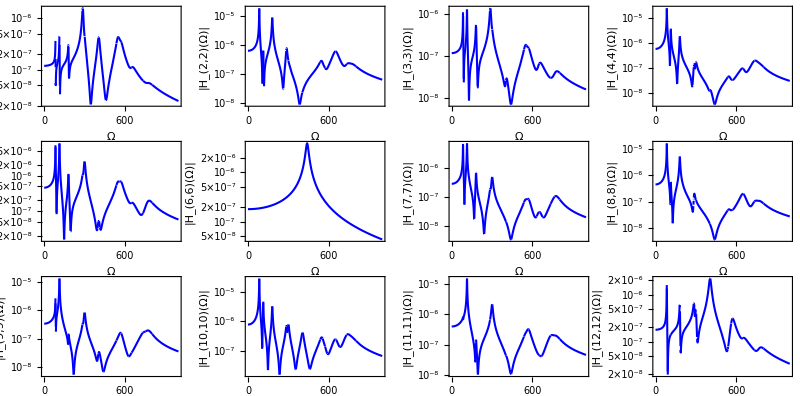

Phase plot for the diagonal elements of the FRF matrix H(Ω):

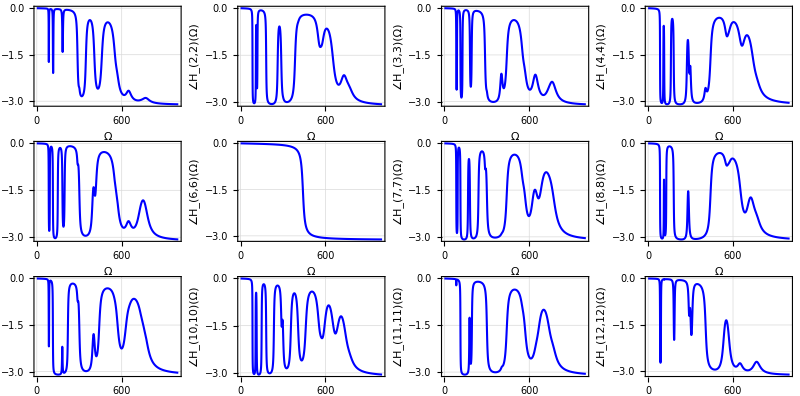

Magnitude plot for the diagonal elements of the accelerance matrix A(Ω):

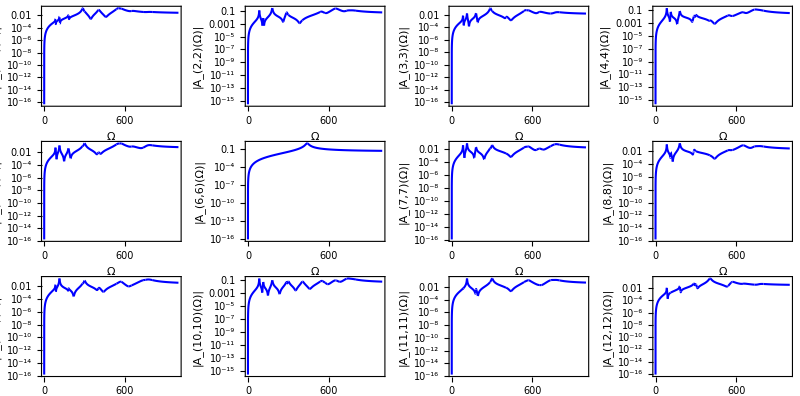

Phase plot for the diagonal elements of the accelerance matrix A(Ω):

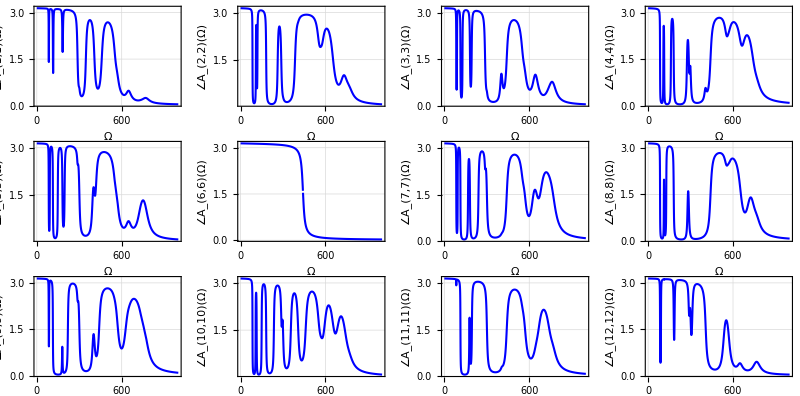

```mathematica
(* Calculate FRF matrix. *)
H = Inverse[-Ω^2*Msystem+I*Ω* Csystem+Ksystem];

(* Plot the magnitude for the diagonal elements of the FRF matrix. *)
Print[Style["Magnitude plot for the diagonal elements of the FRF matrix H(Ω):", Bold, FontFamily->"Times", FontSize->14]]
Plots = Table[LogPlot[Abs[H[[i,i]]], {Ω, 0, 1000}, ImageSize->{300, 200}, PlotStyle->{Directive[Blue, AbsoluteThickness[1.5]]},FrameLabel->{Style["Ω"], Style[Row[{"|",Subscript["H",ToString[i],ToString[i]],"(Ω)|"}]]}, GridLines->Automatic, LabelStyle->{RGBColor[0,0,0], Bold, FontSize->9, FontFamily->"Times"}, PlotRange->All, Frame->True],{i,1,12}];
GraphicsGrid[Partition[Plots,4],ImageSize->800]

(* Plot the phase for the diagonal elements of the FRF matrix. *)
Print[Style["Phase plot for the diagonal elements of the FRF matrix H(Ω):", Bold, FontFamily->"Times", FontSize->14]]
Plots = Table[Plot[FullSimplify[Arg[H[[i,i]]]], {Ω, 0, 1000}, ImageSize->{300, 200}, PlotStyle->{Directive[Blue, AbsoluteThickness[1.5]]},FrameLabel->{Style["Ω"], Style[Row[{"∠",Subscript["H",ToString[i],ToString[i]],"(Ω)"}]]}, GridLines->Automatic, LabelStyle->{RGBColor[0,0,0], Bold, FontSize->9, FontFamily->"Times"}, PlotRange->All, Frame->True],{i,1,12}];
GraphicsGrid[Partition[Plots,4],ImageSize->800]

(* Calculate accelerance matrix. *)
A = -Ω^2*H;

(* Plot the magnitude for the diagonal elements of the accelerance matrix. *)
Print[Style["Magnitude plot for the diagonal elements of the accelerance matrix A(Ω):", Bold, FontFamily->"Times", FontSize->14]]
Plots = Table[LogPlot[Abs[A[[i,i]]], {Ω, 0, 1000}, ImageSize->{300, 200}, PlotStyle->{Directive[Blue, AbsoluteThickness[1.5]]},FrameLabel->{Style["Ω"], Style[Row[{"|",Subscript["A",ToString[i],ToString[i]],"(Ω)|"}]]}, GridLines->Automatic, LabelStyle->{RGBColor[0,0,0], Bold, FontSize->9, FontFamily->"Times"}, PlotRange->All, Frame->True],{i,1,12}];
GraphicsGrid[Partition[Plots,4],ImageSize->800]

(* Plot the phase for the diagonal elements of the accelerance matrix. *)
Print[Style["Phase plot for the diagonal elements of the accelerance matrix A(Ω):", Bold, FontFamily->"Times", FontSize->14]]
Plots = Table[Plot[FullSimplify[Arg[A[[i,i]]]], {Ω, 0, 1000}, ImageSize->{300, 200}, PlotStyle->{Directive[Blue, AbsoluteThickness[1.5]]},FrameLabel->{Style["Ω"], Style[Row[{"∠",Subscript["A",ToString[i],ToString[i]],"(Ω)"}]]}, GridLines->Automatic, LabelStyle->{RGBColor[0,0,0], Bold, FontSize->9, FontFamily->"Times"}, PlotRange->All, Frame->True],{i,1,12}];
GraphicsGrid[Partition[Plots,4],ImageSize->800]
```

## Problem 10

```mathematica
(* Define the force vector in spatial domain. *)
Print[Style["Force vector in spatial domain:", Bold, FontFamily->"Times", FontSize->14]]
Fsystem = {0,0,0,0,30000*Exp[-0.12*t]*Cos[t],20000*Exp[-0.12*t]*Cos[0.5*t],0,0,0,10000*Exp[-0.12*t]*Cos[0.5*t],0,0};
MatrixForm[Fsystem]

(* Tranform the force vector from spatial domain to modal domain. *)
Print[Style["Force vector in modal domain:", Bold, FontFamily->"Times", FontSize->14]]
Fmodal = Dot[Transpose[MassNormalizedModes],Fsystem];
MatrixForm[Fmodal]

(* Show the uncoupled differential equations in modal domain. *)
Print[Style["Uncoupled differential equations in modal domain:", Bold, FontFamily->"Times", FontSize->14]]
Grid[Table[{Row[{"Equation ",i,": "}],q''[t]+2*DampingRatios[[i]]*NaturalFrequencies[[i]]*q'[t]+NaturalFrequencies[[i]]^2*q[t]==Fmodal[[i]]},{i,Length[EigValues]}],Alignment->Left]
```

Force vector in spatial domain:

(0
0
0
0
30000 ⅇ^(-0.12 t) Cos[t]
20000 ⅇ^(-0.12 t) Cos[0.5 t]
0
0
0
10000 ⅇ^(-0.12 t) Cos[0.5 t]
0
0)

Force vector in modal domain:

(0.+597.792 ⅇ^(-0.12 t) Cos[0.5 t]-892.86 ⅇ^(-0.12 t) Cos[t]
0.+322.914 ⅇ^(-0.12 t) Cos[0.5 t]+1316.46 ⅇ^(-0.12 t) Cos[t]
0.-479.908 ⅇ^(-0.12 t) Cos[0.5 t]+851.283 ⅇ^(-0.12 t) Cos[t]
0.+376.989 ⅇ^(-0.12 t) Cos[0.5 t]+886.679 ⅇ^(-0.12 t) Cos[t]
0.-447.004 ⅇ^(-0.12 t) Cos[0.5 t]-2558.51 ⅇ^(-0.12 t) Cos[t]
0.+525.433 ⅇ^(-0.12 t) Cos[0.5 t]-477.69 ⅇ^(-0.12 t) Cos[t]
0.+3726.78 ⅇ^(-0.12 t) Cos[0.5 t]
0.+639.696 ⅇ^(-0.12 t) Cos[0.5 t]-2582.15 ⅇ^(-0.12 t) Cos[t]
0.+252.243 ⅇ^(-0.12 t) Cos[0.5 t]-2852.82 ⅇ^(-0.12 t) Cos[t]
0.+748.151 ⅇ^(-0.12 t) Cos[0.5 t]+1281.13 ⅇ^(-0.12 t) Cos[t]
0.+1124.17 ⅇ^(-0.12 t) Cos[0.5 t]-494.965 ⅇ^(-0.12 t) Cos[t]
0.-555.068 ⅇ^(-0.12 t) Cos[0.5 t]-2531.78 ⅇ^(-0.12 t) Cos[t])

Uncoupled differential equations in modal domain:

Equation 1:  | 7104.22 q[t]+1.41042 q'[t]+q''[t]==0.+597.792 ⅇ^(-0.12 t) Cos[0.5 t]-892.86 ⅇ^(-0.12 t) Cos[t]
Equation 2:  | 12944.1 q[t]+1.99441 q'[t]+q''[t]==0.+322.914 ⅇ^(-0.12 t) Cos[0.5 t]+1316.46 ⅇ^(-0.12 t) Cos[t]
Equation 3:  | 32760.5 q[t]+3.97605 q'[t]+q''[t]==0.-479.908 ⅇ^(-0.12 t) Cos[0.5 t]+851.283 ⅇ^(-0.12 t) Cos[t]
Equation 4:  | 82753.5 q[t]+8.97535 q'[t]+q''[t]==0.+376.989 ⅇ^(-0.12 t) Cos[0.5 t]+886.679 ⅇ^(-0.12 t) Cos[t]
Equation 5:  | 90473. q[t]+9.7473 q'[t]+q''[t]==0.-447.004 ⅇ^(-0.12 t) Cos[0.5 t]-2558.51 ⅇ^(-0.12 t) Cos[t]
Equation 6:  | 165354. q[t]+17.2354 q'[t]+q''[t]==0.+525.433 ⅇ^(-0.12 t) Cos[0.5 t]-477.69 ⅇ^(-0.12 t) Cos[t]
Equation 7:  | 194444. q[t]+20.1444 q'[t]+q''[t]==0.+3726.78 ⅇ^(-0.12 t) Cos[0.5 t]
Equation 8:  | 303972. q[t]+31.0972 q'[t]+q''[t]==0.+639.696 ⅇ^(-0.12 t) Cos[0.5 t]-2582.15 ⅇ^(-0.12 t) Cos[t]
Equation 9:  | 325617. q[t]+33.2617 q'[t]+q''[t]==0.+252.243 ⅇ^(-0.12 t) Cos[0.5 t]-2852.82 ⅇ^(-0.12 t) Cos[t]
Equation 10:  | 425814. q[t]+43.2814 q'[t]+q''[t]==0.+748.151 ⅇ^(-0.12 t) Cos[0.5 t]+1281.13 ⅇ^(-0.12 t) Cos[t]
Equation 11:  | 548135. q[t]+55.5135 q'[t]+q''[t]==0.+1124.17 ⅇ^(-0.12 t) Cos[0.5 t]-494.965 ⅇ^(-0.12 t) Cos[t]
Equation 12:  | 596826. q[t]+60.3826 q'[t]+q''[t]==0.-555.068 ⅇ^(-0.12 t) Cos[0.5 t]-2531.78 ⅇ^(-0.12 t) Cos[t]

## Problem 11

Solutions of uncoupled differential equations q(t) (modal DOF solutions):

(0.0841509 ⅇ^(-0.12 t) Cos[0.5 t]-0.125701 ⅇ^(-0.12 t) Cos[t]+0.0415498 ⅇ^(-0.705211 t) Cos[84.2836 t]+6.93233×10^-6 ⅇ^(-0.12 t) Sin[0.5 t]-0.0000207126 ⅇ^(-0.12 t) Sin[t]+0.0002887 ⅇ^(-0.705211 t) Sin[84.2836 t]
0.0249477 ⅇ^(-0.12 t) Cos[0.5 t]+0.101713 ⅇ^(-0.12 t) Cos[t]-0.126661 ⅇ^(-0.997204 t) Cos[113.768 t]+1.69074×10^-6 ⅇ^(-0.12 t) Sin[0.5 t]+0.0000137873 ⅇ^(-0.12 t) Sin[t]-0.000976747 ⅇ^(-0.997204 t) Sin[113.768 t]
-0.0146493 ⅇ^(-0.12 t) Cos[0.5 t]+0.0259862 ⅇ^(-0.12 t) Cos[t]-0.0113369 ⅇ^(-1.98803 t) Cos[180.988 t]-8.35331×10^-7 ⅇ^(-0.12 t) Sin[0.5 t]+2.96363×10^-6 ⅇ^(-0.12 t) Sin[t]-0.000117025 ⅇ^(-1.98803 t) Sin[180.988 t]
0.00455563 ⅇ^(-0.12 t) Cos[0.5 t]+0.010715 ⅇ^(-0.12 t) Cos[t]-0.0152706 ⅇ^(-4.48768 t) Cos[287.634 t]+2.40447×10^-7 ⅇ^(-0.12 t) Sin[0.5 t]+1.13109×10^-6 ⅇ^(-0.12 t) Sin[t]-0.000231886 ⅇ^(-4.48768 t) Sin[287.634 t]
-0.00494082 ⅇ^(-0.12 t) Cos[0.5 t]-0.0282799 ⅇ^(-0.12 t) Cos[t]+0.0332207 ⅇ^(-4.87365 t) Cos[300.748 t]-2.59606×10^-7 ⅇ^(-0.12 t) Sin[0.5 t]-2.97185×10^-6 ⅇ^(-0.12 t) Sin[t]+0.000525101 ⅇ^(-4.87365 t) Sin[300.748 t]
0.00317767 ⅇ^(-0.12 t) Cos[0.5 t]-0.00288894 ⅇ^(-0.12 t) Cos[t]-0.000288724 ⅇ^(-8.6177 t) Cos[406.546 t]+1.63306×10^-7 ⅇ^(-0.12 t) Sin[0.5 t]-2.96937×10^-7 ⅇ^(-0.12 t) Sin[t]-6.03442×10^-6 ⅇ^(-8.6177 t) Sin[406.546 t]
0.0191666 ⅇ^(-0.12 t) Cos[0.5 t]-0.0191666 ⅇ^(-10.0722 t) Cos[440.844 t]+9.81013×10^-7 ⅇ^(-0.12 t) Sin[0.5 t]-0.000432694 ⅇ^(-10.0722 t) Sin[440.844 t]
0.00210448 ⅇ^(-0.12 t) Cos[0.5 t]-0.00849481 ⅇ^(-0.12 t) Cos[t]+0.00639033 ⅇ^(-15.5486 t) Cos[551.118 t]+1.06818×10^-7 ⅇ^(-0.12 t) Sin[0.5 t]-8.6235×10^-7 ⅇ^(-0.12 t) Sin[t]+0.0001789 ⅇ^(-15.5486 t) Sin[551.118 t]
0.000774673 ⅇ^(-0.12 t) Cos[0.5 t]-0.0087614 ⅇ^(-0.12 t) Cos[t]+0.00798673 ⅇ^(-16.6308 t) Cos[570.386 t]+3.92813×10^-8 ⅇ^(-0.12 t) Sin[0.5 t]-8.88531×10^-7 ⅇ^(-0.12 t) Sin[t]+0.000231192 ⅇ^(-16.6308 t) Sin[570.386 t]
0.00175701 ⅇ^(-0.12 t) Cos[0.5 t]+0.0030087 ⅇ^(-0.12 t) Cos[t]-0.00476572 ⅇ^(-21.6407 t) Cos[652.185 t]+8.88008×10^-8 ⅇ^(-0.12 t) Sin[0.5 t]+3.04125×10^-7 ⅇ^(-0.12 t) Sin[t]-0.000157259 ⅇ^(-21.6407 t) Sin[652.185 t]
0.00205093 ⅇ^(-0.12 t) Cos[0.5 t]-0.000903011 ⅇ^(-0.12 t) Cos[t]-0.00114792 ⅇ^(-27.7568 t) Cos[739.841 t]+1.03408×10^-7 ⅇ^(-0.12 t) Sin[0.5 t]-9.10601×10^-8 ⅇ^(-0.12 t) Sin[t]-0.0000428804 ⅇ^(-27.7568 t) Sin[739.841 t]
-0.000930045 ⅇ^(-0.12 t) Cos[0.5 t]-0.00424213 ⅇ^(-0.12 t) Cos[t]+0.00517218 ⅇ^(-30.1913 t) Cos[771.955 t]-4.68613×10^-8 ⅇ^(-0.12 t) Sin[0.5 t]-4.27489×10^-7 ⅇ^(-0.12 t) Sin[t]+0.000201481 ⅇ^(-30.1913 t) Sin[771.955 t])

Plot for modal DOF solutions q(t):

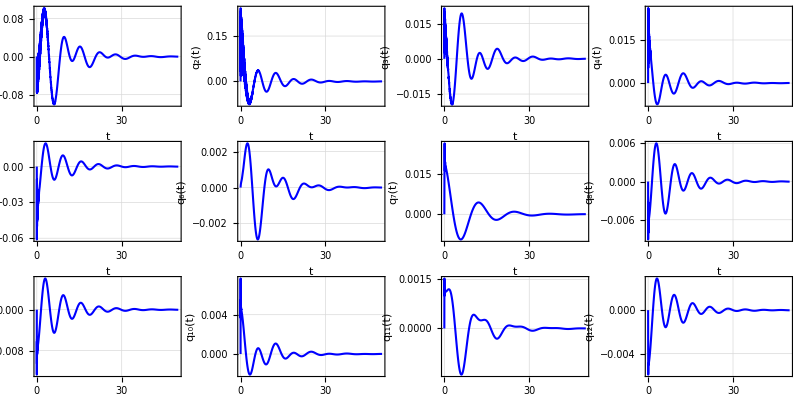

Spatial DOF solutions:

X1(t) =

0.-0.0061178 (0.0841509 ⅇ^(-0.12 t) Cos[0.5 t]-0.125701 ⅇ^(-0.12 t) Cos[t]+0.0415498 ⅇ^(-0.705211 t) Cos[84.2836 t]+6.93233×10^-6 ⅇ^(-0.12 t) Sin[0.5 t]-0.0000207126 ⅇ^(-0.12 t) Sin[t]+0.0002887 ⅇ^(-0.705211 t) Sin[84.2836 t])+0.00968918 (0.0249477 ⅇ^(-0.12 t) Cos[0.5 t]+0.101713 ⅇ^(-0.12 t) Cos[t]-0.126661 ⅇ^(-0.997204 t) Cos[113.768 t]+1.69074×10^-6 ⅇ^(-0.12 t) Sin[0.5 t]+0.0000137873 ⅇ^(-0.12 t) Sin[t]-0.000976747 ⅇ^(-0.997204 t) Sin[113.768 t])-0.0130273 (-0.0146493 ⅇ^(-0.12 t) Cos[0.5 t]+0.0259862 ⅇ^(-0.12 t) Cos[t]-0.0113369 ⅇ^(-1.98803 t) Cos[180.988 t]-8.35331×10^-7 ⅇ^(-0.12 t) Sin[0.5 t]+2.96363×10^-6 ⅇ^(-0.12 t) Sin[t]-0.000117025 ⅇ^(-1.98803 t) Sin[180.988 t])-0.0634375 (0.00455563 ⅇ^(-0.12 t) Cos[0.5 t]+0.010715 ⅇ^(-0.12 t) Cos[t]-0.0152706 ⅇ^(-4.48768 t) Cos[287.634 t]+2.40447×10^-7 ⅇ^(-0.12 t) Sin[0.5 t]+1.13109×10^-6 ⅇ^(-0.12 t) Sin[t]-0.000231886 ⅇ^(-4.48768 t) Sin[287.634 t])-0.0149709 (-0.00494082 ⅇ^(-0.12 t) Cos[0.5 t]-0.0282799 ⅇ^(-0.12 t) Cos[t]+0.0332207 ⅇ^(-4.87365 t) Cos[300.748 t]-2.59606×10^-7 ⅇ^(-0.12 t) Sin[0.5 t]-2.97185×10^-6 ⅇ^(-0.12 t) Sin[t]+0.000525101 ⅇ^(-4.87365 t) Sin[300.748 t])+0.054104 (0.00317767 ⅇ^(-0.12 t) Cos[0.5 t]-0.00288894 ⅇ^(-0.12 t) Cos[t]-0.000288724 ⅇ^(-8.6177 t) Cos[406.546 t]+1.63306×10^-7 ⅇ^(-0.12 t) Sin[0.5 t]-2.96937×10^-7 ⅇ^(-0.12 t) Sin[t]-6.03442×10^-6 ⅇ^(-8.6177 t) Sin[406.546 t])-0.0783938 (0.00210448 ⅇ^(-0.12 t) Cos[0.5 t]-0.00849481 ⅇ^(-0.12 t) Cos[t]+0.00639033 ⅇ^(-15.5486 t) Cos[551.118 t]+1.06818×10^-7 ⅇ^(-0.12 t) Sin[0.5 t]-8.6235×10^-7 ⅇ^(-0.12 t) Sin[t]+0.0001789 ⅇ^(-15.5486 t) Sin[551.118 t])+0.0549149 (0.000774673 ⅇ^(-0.12 t) Cos[0.5 t]-0.0087614 ⅇ^(-0.12 t) Cos[t]+0.00798673 ⅇ^(-16.6308 t) Cos[570.386 t]+3.92813×10^-8 ⅇ^(-0.12 t) Sin[0.5 t]-8.88531×10^-7 ⅇ^(-0.12 t) Sin[t]+0.000231192 ⅇ^(-16.6308 t) Sin[570.386 t])+0.0312719 (0.00175701 ⅇ^(-0.12 t) Cos[0.5 t]+0.0030087 ⅇ^(-0.12 t) Cos[t]-0.00476572 ⅇ^(-21.6407 t) Cos[652.185 t]+8.88008×10^-8 ⅇ^(-0.12 t) Sin[0.5 t]+3.04125×10^-7 ⅇ^(-0.12 t) Sin[t]-0.000157259 ⅇ^(-21.6407 t) Sin[652.185 t])+0.00644546 (0.00205093 ⅇ^(-0.12 t) Cos[0.5 t]-0.000903011 ⅇ^(-0.12 t) Cos[t]-0.00114792 ⅇ^(-27.7568 t) Cos[739.841 t]+1.03408×10^-7 ⅇ^(-0.12 t) Sin[0.5 t]-9.10601×10^-8 ⅇ^(-0.12 t) Sin[t]-0.0000428804 ⅇ^(-27.7568 t) Sin[739.841 t])+0.0202129 (-0.000930045 ⅇ^(-0.12 t) Cos[0.5 t]-0.00424213 ⅇ^(-0.12 t) Cos[t]+0.00517218 ⅇ^(-30.1913 t) Cos[771.955 t]-4.68613×10^-8 ⅇ^(-0.12 t) Sin[0.5 t]-4.27489×10^-7 ⅇ^(-0.12 t) Sin[t]+0.000201481 ⅇ^(-30.1913 t) Sin[771.955 t])

X2(t) =

0.+0.0486286 (0.0841509 ⅇ^(-0.12 t) Cos[0.5 t]-0.125701 ⅇ^(-0.12 t) Cos[t]+0.0415498 ⅇ^(-0.705211 t) Cos[84.2836 t]+6.93233×10^-6 ⅇ^(-0.12 t) Sin[0.5 t]-0.0000207126 ⅇ^(-0.12 t) Sin[t]+0.0002887 ⅇ^(-0.705211 t) Sin[84.2836 t])+0.0120956 (0.0249477 ⅇ^(-0.12 t) Cos[0.5 t]+0.101713 ⅇ^(-0.12 t) Cos[t]-0.126661 ⅇ^(-0.997204 t) Cos[113.768 t]+1.69074×10^-6 ⅇ^(-0.12 t) Sin[0.5 t]+0.0000137873 ⅇ^(-0.12 t) Sin[t]-0.000976747 ⅇ^(-0.997204 t) Sin[113.768 t])+0.0798992 (-0.0146493 ⅇ^(-0.12 t) Cos[0.5 t]+0.0259862 ⅇ^(-0.12 t) Cos[t]-0.0113369 ⅇ^(-1.98803 t) Cos[180.988 t]-8.35331×10^-7 ⅇ^(-0.12 t) Sin[0.5 t]+2.96363×10^-6 ⅇ^(-0.12 t) Sin[t]-0.000117025 ⅇ^(-1.98803 t) Sin[180.988 t])-0.0440978 (0.00455563 ⅇ^(-0.12 t) Cos[0.5 t]+0.010715 ⅇ^(-0.12 t) Cos[t]-0.0152706 ⅇ^(-4.48768 t) Cos[287.634 t]+2.40447×10^-7 ⅇ^(-0.12 t) Sin[0.5 t]+1.13109×10^-6 ⅇ^(-0.12 t) Sin[t]-0.000231886 ⅇ^(-4.48768 t) Sin[287.634 t])+0.00338646 (-0.00494082 ⅇ^(-0.12 t) Cos[0.5 t]-0.0282799 ⅇ^(-0.12 t) Cos[t]+0.0332207 ⅇ^(-4.87365 t) Cos[300.748 t]-2.59606×10^-7 ⅇ^(-0.12 t) Sin[0.5 t]-2.97185×10^-6 ⅇ^(-0.12 t) Sin[t]+0.000525101 ⅇ^(-4.87365 t) Sin[300.748 t])+0.00261564 (0.00317767 ⅇ^(-0.12 t) Cos[0.5 t]-0.00288894 ⅇ^(-0.12 t) Cos[t]-0.000288724 ⅇ^(-8.6177 t) Cos[406.546 t]+1.63306×10^-7 ⅇ^(-0.12 t) Sin[0.5 t]-2.96937×10^-7 ⅇ^(-0.12 t) Sin[t]-6.03442×10^-6 ⅇ^(-8.6177 t) Sin[406.546 t])+0.0560678 (0.00210448 ⅇ^(-0.12 t) Cos[0.5 t]-0.00849481 ⅇ^(-0.12 t) Cos[t]+0.00639033 ⅇ^(-15.5486 t) Cos[551.118 t]+1.06818×10^-7 ⅇ^(-0.12 t) Sin[0.5 t]-8.6235×10^-7 ⅇ^(-0.12 t) Sin[t]+0.0001789 ⅇ^(-15.5486 t) Sin[551.118 t])-0.0299842 (0.000774673 ⅇ^(-0.12 t) Cos[0.5 t]-0.0087614 ⅇ^(-0.12 t) Cos[t]+0.00798673 ⅇ^(-16.6308 t) Cos[570.386 t]+3.92813×10^-8 ⅇ^(-0.12 t) Sin[0.5 t]-8.88531×10^-7 ⅇ^(-0.12 t) Sin[t]+0.000231192 ⅇ^(-16.6308 t) Sin[570.386 t])+0.127425 (0.00175701 ⅇ^(-0.12 t) Cos[0.5 t]+0.0030087 ⅇ^(-0.12 t) Cos[t]-0.00476572 ⅇ^(-21.6407 t) Cos[652.185 t]+8.88008×10^-8 ⅇ^(-0.12 t) Sin[0.5 t]+3.04125×10^-7 ⅇ^(-0.12 t) Sin[t]-0.000157259 ⅇ^(-21.6407 t) Sin[652.185 t])-0.0704746 (0.00205093 ⅇ^(-0.12 t) Cos[0.5 t]-0.000903011 ⅇ^(-0.12 t) Cos[t]-0.00114792 ⅇ^(-27.7568 t) Cos[739.841 t]+1.03408×10^-7 ⅇ^(-0.12 t) Sin[0.5 t]-9.10601×10^-8 ⅇ^(-0.12 t) Sin[t]-0.0000428804 ⅇ^(-27.7568 t) Sin[739.841 t])+0.0531177 (-0.000930045 ⅇ^(-0.12 t) Cos[0.5 t]-0.00424213 ⅇ^(-0.12 t) Cos[t]+0.00517218 ⅇ^(-30.1913 t) Cos[771.955 t]-4.68613×10^-8 ⅇ^(-0.12 t) Sin[0.5 t]-4.27489×10^-7 ⅇ^(-0.12 t) Sin[t]+0.000201481 ⅇ^(-30.1913 t) Sin[771.955 t])

X3(t) =

0.-0.0115771 (0.0841509 ⅇ^(-0.12 t) Cos[0.5 t]-0.125701 ⅇ^(-0.12 t) Cos[t]+0.0415498 ⅇ^(-0.705211 t) Cos[84.2836 t]+6.93233×10^-6 ⅇ^(-0.12 t) Sin[0.5 t]-0.0000207126 ⅇ^(-0.12 t) Sin[t]+0.0002887 ⅇ^(-0.705211 t) Sin[84.2836 t])+0.0175057 (0.0249477 ⅇ^(-0.12 t) Cos[0.5 t]+0.101713 ⅇ^(-0.12 t) Cos[t]-0.126661 ⅇ^(-0.997204 t) Cos[113.768 t]+1.69074×10^-6 ⅇ^(-0.12 t) Sin[0.5 t]+0.0000137873 ⅇ^(-0.12 t) Sin[t]-0.000976747 ⅇ^(-0.997204 t) Sin[113.768 t])-0.0199815 (-0.0146493 ⅇ^(-0.12 t) Cos[0.5 t]+0.0259862 ⅇ^(-0.12 t) Cos[t]-0.0113369 ⅇ^(-1.98803 t) Cos[180.988 t]-8.35331×10^-7 ⅇ^(-0.12 t) Sin[0.5 t]+2.96363×10^-6 ⅇ^(-0.12 t) Sin[t]-0.000117025 ⅇ^(-1.98803 t) Sin[180.988 t])-0.0600912 (0.00455563 ⅇ^(-0.12 t) Cos[0.5 t]+0.010715 ⅇ^(-0.12 t) Cos[t]-0.0152706 ⅇ^(-4.48768 t) Cos[287.634 t]+2.40447×10^-7 ⅇ^(-0.12 t) Sin[0.5 t]+1.13109×10^-6 ⅇ^(-0.12 t) Sin[t]-0.000231886 ⅇ^(-4.48768 t) Sin[287.634 t])-0.0129885 (-0.00494082 ⅇ^(-0.12 t) Cos[0.5 t]-0.0282799 ⅇ^(-0.12 t) Cos[t]+0.0332207 ⅇ^(-4.87365 t) Cos[300.748 t]-2.59606×10^-7 ⅇ^(-0.12 t) Sin[0.5 t]-2.97185×10^-6 ⅇ^(-0.12 t) Sin[t]+0.000525101 ⅇ^(-4.87365 t) Sin[300.748 t])+0.011359 (0.00317767 ⅇ^(-0.12 t) Cos[0.5 t]-0.00288894 ⅇ^(-0.12 t) Cos[t]-0.000288724 ⅇ^(-8.6177 t) Cos[406.546 t]+1.63306×10^-7 ⅇ^(-0.12 t) Sin[0.5 t]-2.96937×10^-7 ⅇ^(-0.12 t) Sin[t]-6.03442×10^-6 ⅇ^(-8.6177 t) Sin[406.546 t])+0.0495701 (0.00210448 ⅇ^(-0.12 t) Cos[0.5 t]-0.00849481 ⅇ^(-0.12 t) Cos[t]+0.00639033 ⅇ^(-15.5486 t) Cos[551.118 t]+1.06818×10^-7 ⅇ^(-0.12 t) Sin[0.5 t]-8.6235×10^-7 ⅇ^(-0.12 t) Sin[t]+0.0001789 ⅇ^(-15.5486 t) Sin[551.118 t])-0.0403262 (0.000774673 ⅇ^(-0.12 t) Cos[0.5 t]-0.0087614 ⅇ^(-0.12 t) Cos[t]+0.00798673 ⅇ^(-16.6308 t) Cos[570.386 t]+3.92813×10^-8 ⅇ^(-0.12 t) Sin[0.5 t]-8.88531×10^-7 ⅇ^(-0.12 t) Sin[t]+0.000231192 ⅇ^(-16.6308 t) Sin[570.386 t])-0.0355239 (0.00175701 ⅇ^(-0.12 t) Cos[0.5 t]+0.0030087 ⅇ^(-0.12 t) Cos[t]-0.00476572 ⅇ^(-21.6407 t) Cos[652.185 t]+8.88008×10^-8 ⅇ^(-0.12 t) Sin[0.5 t]+3.04125×10^-7 ⅇ^(-0.12 t) Sin[t]-0.000157259 ⅇ^(-21.6407 t) Sin[652.185 t])-0.00973165 (0.00205093 ⅇ^(-0.12 t) Cos[0.5 t]-0.000903011 ⅇ^(-0.12 t) Cos[t]-0.00114792 ⅇ^(-27.7568 t) Cos[739.841 t]+1.03408×10^-7 ⅇ^(-0.12 t) Sin[0.5 t]-9.10601×10^-8 ⅇ^(-0.12 t) Sin[t]-0.0000428804 ⅇ^(-27.7568 t) Sin[739.841 t])-0.0330047 (-0.000930045 ⅇ^(-0.12 t) Cos[0.5 t]-0.00424213 ⅇ^(-0.12 t) Cos[t]+0.00517218 ⅇ^(-30.1913 t) Cos[771.955 t]-4.68613×10^-8 ⅇ^(-0.12 t) Sin[0.5 t]-4.27489×10^-7 ⅇ^(-0.12 t) Sin[t]+0.000201481 ⅇ^(-30.1913 t) Sin[771.955 t])

X4(t) =

0.+0.0565619 (0.0841509 ⅇ^(-0.12 t) Cos[0.5 t]-0.125701 ⅇ^(-0.12 t) Cos[t]+0.0415498 ⅇ^(-0.705211 t) Cos[84.2836 t]+6.93233×10^-6 ⅇ^(-0.12 t) Sin[0.5 t]-0.0000207126 ⅇ^(-0.12 t) Sin[t]+0.0002887 ⅇ^(-0.705211 t) Sin[84.2836 t])+0.0291708 (0.0249477 ⅇ^(-0.12 t) Cos[0.5 t]+0.101713 ⅇ^(-0.12 t) Cos[t]-0.126661 ⅇ^(-0.997204 t) Cos[113.768 t]+1.69074×10^-6 ⅇ^(-0.12 t) Sin[0.5 t]+0.0000137873 ⅇ^(-0.12 t) Sin[t]-0.000976747 ⅇ^(-0.997204 t) Sin[113.768 t])-0.0368047 (-0.0146493 ⅇ^(-0.12 t) Cos[0.5 t]+0.0259862 ⅇ^(-0.12 t) Cos[t]-0.0113369 ⅇ^(-1.98803 t) Cos[180.988 t]-8.35331×10^-7 ⅇ^(-0.12 t) Sin[0.5 t]+2.96363×10^-6 ⅇ^(-0.12 t) Sin[t]-0.000117025 ⅇ^(-1.98803 t) Sin[180.988 t])+0.0178551 (0.00455563 ⅇ^(-0.12 t) Cos[0.5 t]+0.010715 ⅇ^(-0.12 t) Cos[t]-0.0152706 ⅇ^(-4.48768 t) Cos[287.634 t]+2.40447×10^-7 ⅇ^(-0.12 t) Sin[0.5 t]+1.13109×10^-6 ⅇ^(-0.12 t) Sin[t]-0.000231886 ⅇ^(-4.48768 t) Sin[287.634 t])-0.0193906 (-0.00494082 ⅇ^(-0.12 t) Cos[0.5 t]-0.0282799 ⅇ^(-0.12 t) Cos[t]+0.0332207 ⅇ^(-4.87365 t) Cos[300.748 t]-2.59606×10^-7 ⅇ^(-0.12 t) Sin[0.5 t]-2.97185×10^-6 ⅇ^(-0.12 t) Sin[t]+0.000525101 ⅇ^(-4.87365 t) Sin[300.748 t])+0.00551566 (0.00317767 ⅇ^(-0.12 t) Cos[0.5 t]-0.00288894 ⅇ^(-0.12 t) Cos[t]-0.000288724 ⅇ^(-8.6177 t) Cos[406.546 t]+1.63306×10^-7 ⅇ^(-0.12 t) Sin[0.5 t]-2.96937×10^-7 ⅇ^(-0.12 t) Sin[t]-6.03442×10^-6 ⅇ^(-8.6177 t) Sin[406.546 t])-0.0202247 (0.00210448 ⅇ^(-0.12 t) Cos[0.5 t]-0.00849481 ⅇ^(-0.12 t) Cos[t]+0.00639033 ⅇ^(-15.5486 t) Cos[551.118 t]+1.06818×10^-7 ⅇ^(-0.12 t) Sin[0.5 t]-8.6235×10^-7 ⅇ^(-0.12 t) Sin[t]+0.0001789 ⅇ^(-15.5486 t) Sin[551.118 t])-0.00926162 (0.000774673 ⅇ^(-0.12 t) Cos[0.5 t]-0.0087614 ⅇ^(-0.12 t) Cos[t]+0.00798673 ⅇ^(-16.6308 t) Cos[570.386 t]+3.92813×10^-8 ⅇ^(-0.12 t) Sin[0.5 t]-8.88531×10^-7 ⅇ^(-0.12 t) Sin[t]+0.000231192 ⅇ^(-16.6308 t) Sin[570.386 t])-0.0424939 (0.00175701 ⅇ^(-0.12 t) Cos[0.5 t]+0.0030087 ⅇ^(-0.12 t) Cos[t]-0.00476572 ⅇ^(-21.6407 t) Cos[652.185 t]+8.88008×10^-8 ⅇ^(-0.12 t) Sin[0.5 t]+3.04125×10^-7 ⅇ^(-0.12 t) Sin[t]-0.000157259 ⅇ^(-21.6407 t) Sin[652.185 t])-0.0848663 (0.00205093 ⅇ^(-0.12 t) Cos[0.5 t]-0.000903011 ⅇ^(-0.12 t) Cos[t]-0.00114792 ⅇ^(-27.7568 t) Cos[739.841 t]+1.03408×10^-7 ⅇ^(-0.12 t) Sin[0.5 t]-9.10601×10^-8 ⅇ^(-0.12 t) Sin[t]-0.0000428804 ⅇ^(-27.7568 t) Sin[739.841 t])+0.0453172 (-0.000930045 ⅇ^(-0.12 t) Cos[0.5 t]-0.00424213 ⅇ^(-0.12 t) Cos[t]+0.00517218 ⅇ^(-30.1913 t) Cos[771.955 t]-4.68613×10^-8 ⅇ^(-0.12 t) Sin[0.5 t]-4.27489×10^-7 ⅇ^(-0.12 t) Sin[t]+0.000201481 ⅇ^(-30.1913 t) Sin[771.955 t])

X5(t) =

0.-0.029762 (0.0841509 ⅇ^(-0.12 t) Cos[0.5 t]-0.125701 ⅇ^(-0.12 t) Cos[t]+0.0415498 ⅇ^(-0.705211 t) Cos[84.2836 t]+6.93233×10^-6 ⅇ^(-0.12 t) Sin[0.5 t]-0.0000207126 ⅇ^(-0.12 t) Sin[t]+0.0002887 ⅇ^(-0.705211 t) Sin[84.2836 t])+0.043882 (0.0249477 ⅇ^(-0.12 t) Cos[0.5 t]+0.101713 ⅇ^(-0.12 t) Cos[t]-0.126661 ⅇ^(-0.997204 t) Cos[113.768 t]+1.69074×10^-6 ⅇ^(-0.12 t) Sin[0.5 t]+0.0000137873 ⅇ^(-0.12 t) Sin[t]-0.000976747 ⅇ^(-0.997204 t) Sin[113.768 t])+0.0283761 (-0.0146493 ⅇ^(-0.12 t) Cos[0.5 t]+0.0259862 ⅇ^(-0.12 t) Cos[t]-0.0113369 ⅇ^(-1.98803 t) Cos[180.988 t]-8.35331×10^-7 ⅇ^(-0.12 t) Sin[0.5 t]+2.96363×10^-6 ⅇ^(-0.12 t) Sin[t]-0.000117025 ⅇ^(-1.98803 t) Sin[180.988 t])+0.029556 (0.00455563 ⅇ^(-0.12 t) Cos[0.5 t]+0.010715 ⅇ^(-0.12 t) Cos[t]-0.0152706 ⅇ^(-4.48768 t) Cos[287.634 t]+2.40447×10^-7 ⅇ^(-0.12 t) Sin[0.5 t]+1.13109×10^-6 ⅇ^(-0.12 t) Sin[t]-0.000231886 ⅇ^(-4.48768 t) Sin[287.634 t])-0.0852836 (-0.00494082 ⅇ^(-0.12 t) Cos[0.5 t]-0.0282799 ⅇ^(-0.12 t) Cos[t]+0.0332207 ⅇ^(-4.87365 t) Cos[300.748 t]-2.59606×10^-7 ⅇ^(-0.12 t) Sin[0.5 t]-2.97185×10^-6 ⅇ^(-0.12 t) Sin[t]+0.000525101 ⅇ^(-4.87365 t) Sin[300.748 t])-0.015923 (0.00317767 ⅇ^(-0.12 t) Cos[0.5 t]-0.00288894 ⅇ^(-0.12 t) Cos[t]-0.000288724 ⅇ^(-8.6177 t) Cos[406.546 t]+1.63306×10^-7 ⅇ^(-0.12 t) Sin[0.5 t]-2.96937×10^-7 ⅇ^(-0.12 t) Sin[t]-6.03442×10^-6 ⅇ^(-8.6177 t) Sin[406.546 t])-0.0860716 (0.00210448 ⅇ^(-0.12 t) Cos[0.5 t]-0.00849481 ⅇ^(-0.12 t) Cos[t]+0.00639033 ⅇ^(-15.5486 t) Cos[551.118 t]+1.06818×10^-7 ⅇ^(-0.12 t) Sin[0.5 t]-8.6235×10^-7 ⅇ^(-0.12 t) Sin[t]+0.0001789 ⅇ^(-15.5486 t) Sin[551.118 t])-0.095094 (0.000774673 ⅇ^(-0.12 t) Cos[0.5 t]-0.0087614 ⅇ^(-0.12 t) Cos[t]+0.00798673 ⅇ^(-16.6308 t) Cos[570.386 t]+3.92813×10^-8 ⅇ^(-0.12 t) Sin[0.5 t]-8.88531×10^-7 ⅇ^(-0.12 t) Sin[t]+0.000231192 ⅇ^(-16.6308 t) Sin[570.386 t])+0.0427043 (0.00175701 ⅇ^(-0.12 t) Cos[0.5 t]+0.0030087 ⅇ^(-0.12 t) Cos[t]-0.00476572 ⅇ^(-21.6407 t) Cos[652.185 t]+8.88008×10^-8 ⅇ^(-0.12 t) Sin[0.5 t]+3.04125×10^-7 ⅇ^(-0.12 t) Sin[t]-0.000157259 ⅇ^(-21.6407 t) Sin[652.185 t])-0.0164988 (0.00205093 ⅇ^(-0.12 t) Cos[0.5 t]-0.000903011 ⅇ^(-0.12 t) Cos[t]-0.00114792 ⅇ^(-27.7568 t) Cos[739.841 t]+1.03408×10^-7 ⅇ^(-0.12 t) Sin[0.5 t]-9.10601×10^-8 ⅇ^(-0.12 t) Sin[t]-0.0000428804 ⅇ^(-27.7568 t) Sin[739.841 t])-0.0843927 (-0.000930045 ⅇ^(-0.12 t) Cos[0.5 t]-0.00424213 ⅇ^(-0.12 t) Cos[t]+0.00517218 ⅇ^(-30.1913 t) Cos[771.955 t]-4.68613×10^-8 ⅇ^(-0.12 t) Sin[0.5 t]-4.27489×10^-7 ⅇ^(-0.12 t) Sin[t]+0.000201481 ⅇ^(-30.1913 t) Sin[771.955 t])

X6(t) =

0.+0.186339 (0.0191666 ⅇ^(-0.12 t) Cos[0.5 t]-0.0191666 ⅇ^(-10.0722 t) Cos[440.844 t]+9.81013×10^-7 ⅇ^(-0.12 t) Sin[0.5 t]-0.000432694 ⅇ^(-10.0722 t) Sin[440.844 t])

X7(t) =

0.-0.0281602 (0.0841509 ⅇ^(-0.12 t) Cos[0.5 t]-0.125701 ⅇ^(-0.12 t) Cos[t]+0.0415498 ⅇ^(-0.705211 t) Cos[84.2836 t]+6.93233×10^-6 ⅇ^(-0.12 t) Sin[0.5 t]-0.0000207126 ⅇ^(-0.12 t) Sin[t]+0.0002887 ⅇ^(-0.705211 t) Sin[84.2836 t])+0.0396413 (0.0249477 ⅇ^(-0.12 t) Cos[0.5 t]+0.101713 ⅇ^(-0.12 t) Cos[t]-0.126661 ⅇ^(-0.997204 t) Cos[113.768 t]+1.69074×10^-6 ⅇ^(-0.12 t) Sin[0.5 t]+0.0000137873 ⅇ^(-0.12 t) Sin[t]-0.000976747 ⅇ^(-0.997204 t) Sin[113.768 t])+0.021762 (-0.0146493 ⅇ^(-0.12 t) Cos[0.5 t]+0.0259862 ⅇ^(-0.12 t) Cos[t]-0.0113369 ⅇ^(-1.98803 t) Cos[180.988 t]-8.35331×10^-7 ⅇ^(-0.12 t) Sin[0.5 t]+2.96363×10^-6 ⅇ^(-0.12 t) Sin[t]-0.000117025 ⅇ^(-1.98803 t) Sin[180.988 t])+0.0139985 (0.00455563 ⅇ^(-0.12 t) Cos[0.5 t]+0.010715 ⅇ^(-0.12 t) Cos[t]-0.0152706 ⅇ^(-4.48768 t) Cos[287.634 t]+2.40447×10^-7 ⅇ^(-0.12 t) Sin[0.5 t]+1.13109×10^-6 ⅇ^(-0.12 t) Sin[t]-0.000231886 ⅇ^(-4.48768 t) Sin[287.634 t])-0.0369953 (-0.00494082 ⅇ^(-0.12 t) Cos[0.5 t]-0.0282799 ⅇ^(-0.12 t) Cos[t]+0.0332207 ⅇ^(-4.87365 t) Cos[300.748 t]-2.59606×10^-7 ⅇ^(-0.12 t) Sin[0.5 t]-2.97185×10^-6 ⅇ^(-0.12 t) Sin[t]+0.000525101 ⅇ^(-4.87365 t) Sin[300.748 t])-0.00167149 (0.00317767 ⅇ^(-0.12 t) Cos[0.5 t]-0.00288894 ⅇ^(-0.12 t) Cos[t]-0.000288724 ⅇ^(-8.6177 t) Cos[406.546 t]+1.63306×10^-7 ⅇ^(-0.12 t) Sin[0.5 t]-2.96937×10^-7 ⅇ^(-0.12 t) Sin[t]-6.03442×10^-6 ⅇ^(-8.6177 t) Sin[406.546 t])+0.0272125 (0.00210448 ⅇ^(-0.12 t) Cos[0.5 t]-0.00849481 ⅇ^(-0.12 t) Cos[t]+0.00639033 ⅇ^(-15.5486 t) Cos[551.118 t]+1.06818×10^-7 ⅇ^(-0.12 t) Sin[0.5 t]-8.6235×10^-7 ⅇ^(-0.12 t) Sin[t]+0.0001789 ⅇ^(-15.5486 t) Sin[551.118 t])+0.0349156 (0.000774673 ⅇ^(-0.12 t) Cos[0.5 t]-0.0087614 ⅇ^(-0.12 t) Cos[t]+0.00798673 ⅇ^(-16.6308 t) Cos[570.386 t]+3.92813×10^-8 ⅇ^(-0.12 t) Sin[0.5 t]-8.88531×10^-7 ⅇ^(-0.12 t) Sin[t]+0.000231192 ⅇ^(-16.6308 t) Sin[570.386 t])-0.0242554 (0.00175701 ⅇ^(-0.12 t) Cos[0.5 t]+0.0030087 ⅇ^(-0.12 t) Cos[t]-0.00476572 ⅇ^(-21.6407 t) Cos[652.185 t]+8.88008×10^-8 ⅇ^(-0.12 t) Sin[0.5 t]+3.04125×10^-7 ⅇ^(-0.12 t) Sin[t]-0.000157259 ⅇ^(-21.6407 t) Sin[652.185 t])+0.0124553 (0.00205093 ⅇ^(-0.12 t) Cos[0.5 t]-0.000903011 ⅇ^(-0.12 t) Cos[t]-0.00114792 ⅇ^(-27.7568 t) Cos[739.841 t]+1.03408×10^-7 ⅇ^(-0.12 t) Sin[0.5 t]-9.10601×10^-8 ⅇ^(-0.12 t) Sin[t]-0.0000428804 ⅇ^(-27.7568 t) Sin[739.841 t])+0.0689003 (-0.000930045 ⅇ^(-0.12 t) Cos[0.5 t]-0.00424213 ⅇ^(-0.12 t) Cos[t]+0.00517218 ⅇ^(-30.1913 t) Cos[771.955 t]-4.68613×10^-8 ⅇ^(-0.12 t) Sin[0.5 t]-4.27489×10^-7 ⅇ^(-0.12 t) Sin[t]+0.000201481 ⅇ^(-30.1913 t) Sin[771.955 t])

X8(t) =

0.+0.0460114 (0.0841509 ⅇ^(-0.12 t) Cos[0.5 t]-0.125701 ⅇ^(-0.12 t) Cos[t]+0.0415498 ⅇ^(-0.705211 t) Cos[84.2836 t]+6.93233×10^-6 ⅇ^(-0.12 t) Sin[0.5 t]-0.0000207126 ⅇ^(-0.12 t) Sin[t]+0.0002887 ⅇ^(-0.705211 t) Sin[84.2836 t])+0.0109267 (0.0249477 ⅇ^(-0.12 t) Cos[0.5 t]+0.101713 ⅇ^(-0.12 t) Cos[t]-0.126661 ⅇ^(-0.997204 t) Cos[113.768 t]+1.69074×10^-6 ⅇ^(-0.12 t) Sin[0.5 t]+0.0000137873 ⅇ^(-0.12 t) Sin[t]-0.000976747 ⅇ^(-0.997204 t) Sin[113.768 t])+0.0612756 (-0.0146493 ⅇ^(-0.12 t) Cos[0.5 t]+0.0259862 ⅇ^(-0.12 t) Cos[t]-0.0113369 ⅇ^(-1.98803 t) Cos[180.988 t]-8.35331×10^-7 ⅇ^(-0.12 t) Sin[0.5 t]+2.96363×10^-6 ⅇ^(-0.12 t) Sin[t]-0.000117025 ⅇ^(-1.98803 t) Sin[180.988 t])-0.0208859 (0.00455563 ⅇ^(-0.12 t) Cos[0.5 t]+0.010715 ⅇ^(-0.12 t) Cos[t]-0.0152706 ⅇ^(-4.48768 t) Cos[287.634 t]+2.40447×10^-7 ⅇ^(-0.12 t) Sin[0.5 t]+1.13109×10^-6 ⅇ^(-0.12 t) Sin[t]-0.000231886 ⅇ^(-4.48768 t) Sin[287.634 t])+0.00146902 (-0.00494082 ⅇ^(-0.12 t) Cos[0.5 t]-0.0282799 ⅇ^(-0.12 t) Cos[t]+0.0332207 ⅇ^(-4.87365 t) Cos[300.748 t]-2.59606×10^-7 ⅇ^(-0.12 t) Sin[0.5 t]-2.97185×10^-6 ⅇ^(-0.12 t) Sin[t]+0.000525101 ⅇ^(-4.87365 t) Sin[300.748 t])+0.000274573 (0.00317767 ⅇ^(-0.12 t) Cos[0.5 t]-0.00288894 ⅇ^(-0.12 t) Cos[t]-0.000288724 ⅇ^(-8.6177 t) Cos[406.546 t]+1.63306×10^-7 ⅇ^(-0.12 t) Sin[0.5 t]-2.96937×10^-7 ⅇ^(-0.12 t) Sin[t]-6.03442×10^-6 ⅇ^(-8.6177 t) Sin[406.546 t])-0.0177265 (0.00210448 ⅇ^(-0.12 t) Cos[0.5 t]-0.00849481 ⅇ^(-0.12 t) Cos[t]+0.00639033 ⅇ^(-15.5486 t) Cos[551.118 t]+1.06818×10^-7 ⅇ^(-0.12 t) Sin[0.5 t]-8.6235×10^-7 ⅇ^(-0.12 t) Sin[t]+0.0001789 ⅇ^(-15.5486 t) Sin[551.118 t])+0.0110093 (0.000774673 ⅇ^(-0.12 t) Cos[0.5 t]-0.0087614 ⅇ^(-0.12 t) Cos[t]+0.00798673 ⅇ^(-16.6308 t) Cos[570.386 t]+3.92813×10^-8 ⅇ^(-0.12 t) Sin[0.5 t]-8.88531×10^-7 ⅇ^(-0.12 t) Sin[t]+0.000231192 ⅇ^(-16.6308 t) Sin[570.386 t])-0.0723756 (0.00175701 ⅇ^(-0.12 t) Cos[0.5 t]+0.0030087 ⅇ^(-0.12 t) Cos[t]-0.00476572 ⅇ^(-21.6407 t) Cos[652.185 t]+8.88008×10^-8 ⅇ^(-0.12 t) Sin[0.5 t]+3.04125×10^-7 ⅇ^(-0.12 t) Sin[t]-0.000157259 ⅇ^(-21.6407 t) Sin[652.185 t])+0.0532029 (0.00205093 ⅇ^(-0.12 t) Cos[0.5 t]-0.000903011 ⅇ^(-0.12 t) Cos[t]-0.00114792 ⅇ^(-27.7568 t) Cos[739.841 t]+1.03408×10^-7 ⅇ^(-0.12 t) Sin[0.5 t]-9.10601×10^-8 ⅇ^(-0.12 t) Sin[t]-0.0000428804 ⅇ^(-27.7568 t) Sin[739.841 t])-0.0433667 (-0.000930045 ⅇ^(-0.12 t) Cos[0.5 t]-0.00424213 ⅇ^(-0.12 t) Cos[t]+0.00517218 ⅇ^(-30.1913 t) Cos[771.955 t]-4.68613×10^-8 ⅇ^(-0.12 t) Sin[0.5 t]-4.27489×10^-7 ⅇ^(-0.12 t) Sin[t]+0.000201481 ⅇ^(-30.1913 t) Sin[771.955 t])

X9(t) =

0.-0.0171303 (0.0841509 ⅇ^(-0.12 t) Cos[0.5 t]-0.125701 ⅇ^(-0.12 t) Cos[t]+0.0415498 ⅇ^(-0.705211 t) Cos[84.2836 t]+6.93233×10^-6 ⅇ^(-0.12 t) Sin[0.5 t]-0.0000207126 ⅇ^(-0.12 t) Sin[t]+0.0002887 ⅇ^(-0.705211 t) Sin[84.2836 t])+0.055512 (0.0249477 ⅇ^(-0.12 t) Cos[0.5 t]+0.101713 ⅇ^(-0.12 t) Cos[t]-0.126661 ⅇ^(-0.997204 t) Cos[113.768 t]+1.69074×10^-6 ⅇ^(-0.12 t) Sin[0.5 t]+0.0000137873 ⅇ^(-0.12 t) Sin[t]-0.000976747 ⅇ^(-0.997204 t) Sin[113.768 t])+0.00800298 (-0.0146493 ⅇ^(-0.12 t) Cos[0.5 t]+0.0259862 ⅇ^(-0.12 t) Cos[t]-0.0113369 ⅇ^(-1.98803 t) Cos[180.988 t]-8.35331×10^-7 ⅇ^(-0.12 t) Sin[0.5 t]+2.96363×10^-6 ⅇ^(-0.12 t) Sin[t]-0.000117025 ⅇ^(-1.98803 t) Sin[180.988 t])+0.0173122 (0.00455563 ⅇ^(-0.12 t) Cos[0.5 t]+0.010715 ⅇ^(-0.12 t) Cos[t]-0.0152706 ⅇ^(-4.48768 t) Cos[287.634 t]+2.40447×10^-7 ⅇ^(-0.12 t) Sin[0.5 t]+1.13109×10^-6 ⅇ^(-0.12 t) Sin[t]-0.000231886 ⅇ^(-4.48768 t) Sin[287.634 t])+0.0490232 (-0.00494082 ⅇ^(-0.12 t) Cos[0.5 t]-0.0282799 ⅇ^(-0.12 t) Cos[t]+0.0332207 ⅇ^(-4.87365 t) Cos[300.748 t]-2.59606×10^-7 ⅇ^(-0.12 t) Sin[0.5 t]-2.97185×10^-6 ⅇ^(-0.12 t) Sin[t]+0.000525101 ⅇ^(-4.87365 t) Sin[300.748 t])+0.0134709 (0.00317767 ⅇ^(-0.12 t) Cos[0.5 t]-0.00288894 ⅇ^(-0.12 t) Cos[t]-0.000288724 ⅇ^(-8.6177 t) Cos[406.546 t]+1.63306×10^-7 ⅇ^(-0.12 t) Sin[0.5 t]-2.96937×10^-7 ⅇ^(-0.12 t) Sin[t]-6.03442×10^-6 ⅇ^(-8.6177 t) Sin[406.546 t])+0.0103949 (0.00210448 ⅇ^(-0.12 t) Cos[0.5 t]-0.00849481 ⅇ^(-0.12 t) Cos[t]+0.00639033 ⅇ^(-15.5486 t) Cos[551.118 t]+1.06818×10^-7 ⅇ^(-0.12 t) Sin[0.5 t]-8.6235×10^-7 ⅇ^(-0.12 t) Sin[t]+0.0001789 ⅇ^(-15.5486 t) Sin[551.118 t])+0.0538743 (0.000774673 ⅇ^(-0.12 t) Cos[0.5 t]-0.0087614 ⅇ^(-0.12 t) Cos[t]+0.00798673 ⅇ^(-16.6308 t) Cos[570.386 t]+3.92813×10^-8 ⅇ^(-0.12 t) Sin[0.5 t]-8.88531×10^-7 ⅇ^(-0.12 t) Sin[t]+0.000231192 ⅇ^(-16.6308 t) Sin[570.386 t])+0.00876701 (0.00175701 ⅇ^(-0.12 t) Cos[0.5 t]+0.0030087 ⅇ^(-0.12 t) Cos[t]-0.00476572 ⅇ^(-21.6407 t) Cos[652.185 t]+8.88008×10^-8 ⅇ^(-0.12 t) Sin[0.5 t]+3.04125×10^-7 ⅇ^(-0.12 t) Sin[t]-0.000157259 ⅇ^(-21.6407 t) Sin[652.185 t])-0.0613632 (0.00205093 ⅇ^(-0.12 t) Cos[0.5 t]-0.000903011 ⅇ^(-0.12 t) Cos[t]-0.00114792 ⅇ^(-27.7568 t) Cos[739.841 t]+1.03408×10^-7 ⅇ^(-0.12 t) Sin[0.5 t]-9.10601×10^-8 ⅇ^(-0.12 t) Sin[t]-0.0000428804 ⅇ^(-27.7568 t) Sin[739.841 t])-0.0824278 (-0.000930045 ⅇ^(-0.12 t) Cos[0.5 t]-0.00424213 ⅇ^(-0.12 t) Cos[t]+0.00517218 ⅇ^(-30.1913 t) Cos[771.955 t]-4.68613×10^-8 ⅇ^(-0.12 t) Sin[0.5 t]-4.27489×10^-7 ⅇ^(-0.12 t) Sin[t]+0.000201481 ⅇ^(-30.1913 t) Sin[771.955 t])

X10(t) =

0.+0.0597792 (0.0841509 ⅇ^(-0.12 t) Cos[0.5 t]-0.125701 ⅇ^(-0.12 t) Cos[t]+0.0415498 ⅇ^(-0.705211 t) Cos[84.2836 t]+6.93233×10^-6 ⅇ^(-0.12 t) Sin[0.5 t]-0.0000207126 ⅇ^(-0.12 t) Sin[t]+0.0002887 ⅇ^(-0.705211 t) Sin[84.2836 t])+0.0322914 (0.0249477 ⅇ^(-0.12 t) Cos[0.5 t]+0.101713 ⅇ^(-0.12 t) Cos[t]-0.126661 ⅇ^(-0.997204 t) Cos[113.768 t]+1.69074×10^-6 ⅇ^(-0.12 t) Sin[0.5 t]+0.0000137873 ⅇ^(-0.12 t) Sin[t]-0.000976747 ⅇ^(-0.997204 t) Sin[113.768 t])-0.0479908 (-0.0146493 ⅇ^(-0.12 t) Cos[0.5 t]+0.0259862 ⅇ^(-0.12 t) Cos[t]-0.0113369 ⅇ^(-1.98803 t) Cos[180.988 t]-8.35331×10^-7 ⅇ^(-0.12 t) Sin[0.5 t]+2.96363×10^-6 ⅇ^(-0.12 t) Sin[t]-0.000117025 ⅇ^(-1.98803 t) Sin[180.988 t])+0.0376989 (0.00455563 ⅇ^(-0.12 t) Cos[0.5 t]+0.010715 ⅇ^(-0.12 t) Cos[t]-0.0152706 ⅇ^(-4.48768 t) Cos[287.634 t]+2.40447×10^-7 ⅇ^(-0.12 t) Sin[0.5 t]+1.13109×10^-6 ⅇ^(-0.12 t) Sin[t]-0.000231886 ⅇ^(-4.48768 t) Sin[287.634 t])-0.0447004 (-0.00494082 ⅇ^(-0.12 t) Cos[0.5 t]-0.0282799 ⅇ^(-0.12 t) Cos[t]+0.0332207 ⅇ^(-4.87365 t) Cos[300.748 t]-2.59606×10^-7 ⅇ^(-0.12 t) Sin[0.5 t]-2.97185×10^-6 ⅇ^(-0.12 t) Sin[t]+0.000525101 ⅇ^(-4.87365 t) Sin[300.748 t])+0.0525433 (0.00317767 ⅇ^(-0.12 t) Cos[0.5 t]-0.00288894 ⅇ^(-0.12 t) Cos[t]-0.000288724 ⅇ^(-8.6177 t) Cos[406.546 t]+1.63306×10^-7 ⅇ^(-0.12 t) Sin[0.5 t]-2.96937×10^-7 ⅇ^(-0.12 t) Sin[t]-6.03442×10^-6 ⅇ^(-8.6177 t) Sin[406.546 t])+0.0639696 (0.00210448 ⅇ^(-0.12 t) Cos[0.5 t]-0.00849481 ⅇ^(-0.12 t) Cos[t]+0.00639033 ⅇ^(-15.5486 t) Cos[551.118 t]+1.06818×10^-7 ⅇ^(-0.12 t) Sin[0.5 t]-8.6235×10^-7 ⅇ^(-0.12 t) Sin[t]+0.0001789 ⅇ^(-15.5486 t) Sin[551.118 t])+0.0252243 (0.000774673 ⅇ^(-0.12 t) Cos[0.5 t]-0.0087614 ⅇ^(-0.12 t) Cos[t]+0.00798673 ⅇ^(-16.6308 t) Cos[570.386 t]+3.92813×10^-8 ⅇ^(-0.12 t) Sin[0.5 t]-8.88531×10^-7 ⅇ^(-0.12 t) Sin[t]+0.000231192 ⅇ^(-16.6308 t) Sin[570.386 t])+0.0748151 (0.00175701 ⅇ^(-0.12 t) Cos[0.5 t]+0.0030087 ⅇ^(-0.12 t) Cos[t]-0.00476572 ⅇ^(-21.6407 t) Cos[652.185 t]+8.88008×10^-8 ⅇ^(-0.12 t) Sin[0.5 t]+3.04125×10^-7 ⅇ^(-0.12 t) Sin[t]-0.000157259 ⅇ^(-21.6407 t) Sin[652.185 t])+0.112417 (0.00205093 ⅇ^(-0.12 t) Cos[0.5 t]-0.000903011 ⅇ^(-0.12 t) Cos[t]-0.00114792 ⅇ^(-27.7568 t) Cos[739.841 t]+1.03408×10^-7 ⅇ^(-0.12 t) Sin[0.5 t]-9.10601×10^-8 ⅇ^(-0.12 t) Sin[t]-0.0000428804 ⅇ^(-27.7568 t) Sin[739.841 t])-0.0555068 (-0.000930045 ⅇ^(-0.12 t) Cos[0.5 t]-0.00424213 ⅇ^(-0.12 t) Cos[t]+0.00517218 ⅇ^(-30.1913 t) Cos[771.955 t]-4.68613×10^-8 ⅇ^(-0.12 t) Sin[0.5 t]-4.27489×10^-7 ⅇ^(-0.12 t) Sin[t]+0.000201481 ⅇ^(-30.1913 t) Sin[771.955 t])

X11(t) =

0.-0.00425654 (0.0841509 ⅇ^(-0.12 t) Cos[0.5 t]-0.125701 ⅇ^(-0.12 t) Cos[t]+0.0415498 ⅇ^(-0.705211 t) Cos[84.2836 t]+6.93233×10^-6 ⅇ^(-0.12 t) Sin[0.5 t]-0.0000207126 ⅇ^(-0.12 t) Sin[t]+0.0002887 ⅇ^(-0.705211 t) Sin[84.2836 t])+0.0606536 (0.0249477 ⅇ^(-0.12 t) Cos[0.5 t]+0.101713 ⅇ^(-0.12 t) Cos[t]-0.126661 ⅇ^(-0.997204 t) Cos[113.768 t]+1.69074×10^-6 ⅇ^(-0.12 t) Sin[0.5 t]+0.0000137873 ⅇ^(-0.12 t) Sin[t]-0.000976747 ⅇ^(-0.997204 t) Sin[113.768 t])-0.00948681 (-0.0146493 ⅇ^(-0.12 t) Cos[0.5 t]+0.0259862 ⅇ^(-0.12 t) Cos[t]-0.0113369 ⅇ^(-1.98803 t) Cos[180.988 t]-8.35331×10^-7 ⅇ^(-0.12 t) Sin[0.5 t]+2.96363×10^-6 ⅇ^(-0.12 t) Sin[t]-0.000117025 ⅇ^(-1.98803 t) Sin[180.988 t])+0.00240058 (0.00455563 ⅇ^(-0.12 t) Cos[0.5 t]+0.010715 ⅇ^(-0.12 t) Cos[t]-0.0152706 ⅇ^(-4.48768 t) Cos[287.634 t]+2.40447×10^-7 ⅇ^(-0.12 t) Sin[0.5 t]+1.13109×10^-6 ⅇ^(-0.12 t) Sin[t]-0.000231886 ⅇ^(-4.48768 t) Sin[287.634 t])+0.0795269 (-0.00494082 ⅇ^(-0.12 t) Cos[0.5 t]-0.0282799 ⅇ^(-0.12 t) Cos[t]+0.0332207 ⅇ^(-4.87365 t) Cos[300.748 t]-2.59606×10^-7 ⅇ^(-0.12 t) Sin[0.5 t]-2.97185×10^-6 ⅇ^(-0.12 t) Sin[t]+0.000525101 ⅇ^(-4.87365 t) Sin[300.748 t])+0.00449968 (0.00317767 ⅇ^(-0.12 t) Cos[0.5 t]-0.00288894 ⅇ^(-0.12 t) Cos[t]-0.000288724 ⅇ^(-8.6177 t) Cos[406.546 t]+1.63306×10^-7 ⅇ^(-0.12 t) Sin[0.5 t]-2.96937×10^-7 ⅇ^(-0.12 t) Sin[t]-6.03442×10^-6 ⅇ^(-8.6177 t) Sin[406.546 t])-0.0337854 (0.00210448 ⅇ^(-0.12 t) Cos[0.5 t]-0.00849481 ⅇ^(-0.12 t) Cos[t]+0.00639033 ⅇ^(-15.5486 t) Cos[551.118 t]+1.06818×10^-7 ⅇ^(-0.12 t) Sin[0.5 t]-8.6235×10^-7 ⅇ^(-0.12 t) Sin[t]+0.0001789 ⅇ^(-15.5486 t) Sin[551.118 t])-0.0744777 (0.000774673 ⅇ^(-0.12 t) Cos[0.5 t]-0.0087614 ⅇ^(-0.12 t) Cos[t]+0.00798673 ⅇ^(-16.6308 t) Cos[570.386 t]+3.92813×10^-8 ⅇ^(-0.12 t) Sin[0.5 t]-8.88531×10^-7 ⅇ^(-0.12 t) Sin[t]+0.000231192 ⅇ^(-16.6308 t) Sin[570.386 t])+0.0142963 (0.00175701 ⅇ^(-0.12 t) Cos[0.5 t]+0.0030087 ⅇ^(-0.12 t) Cos[t]-0.00476572 ⅇ^(-21.6407 t) Cos[652.185 t]+8.88008×10^-8 ⅇ^(-0.12 t) Sin[0.5 t]+3.04125×10^-7 ⅇ^(-0.12 t) Sin[t]-0.000157259 ⅇ^(-21.6407 t) Sin[652.185 t])+0.0801936 (0.00205093 ⅇ^(-0.12 t) Cos[0.5 t]-0.000903011 ⅇ^(-0.12 t) Cos[t]-0.00114792 ⅇ^(-27.7568 t) Cos[739.841 t]+1.03408×10^-7 ⅇ^(-0.12 t) Sin[0.5 t]-9.10601×10^-8 ⅇ^(-0.12 t) Sin[t]-0.0000428804 ⅇ^(-27.7568 t) Sin[739.841 t])+0.065692 (-0.000930045 ⅇ^(-0.12 t) Cos[0.5 t]-0.00424213 ⅇ^(-0.12 t) Cos[t]+0.00517218 ⅇ^(-30.1913 t) Cos[771.955 t]-4.68613×10^-8 ⅇ^(-0.12 t) Sin[0.5 t]-4.27489×10^-7 ⅇ^(-0.12 t) Sin[t]+0.000201481 ⅇ^(-30.1913 t) Sin[771.955 t])

X12(t) =

0.+0.0138482 (0.0841509 ⅇ^(-0.12 t) Cos[0.5 t]-0.125701 ⅇ^(-0.12 t) Cos[t]+0.0415498 ⅇ^(-0.705211 t) Cos[84.2836 t]+6.93233×10^-6 ⅇ^(-0.12 t) Sin[0.5 t]-0.0000207126 ⅇ^(-0.12 t) Sin[t]+0.0002887 ⅇ^(-0.705211 t) Sin[84.2836 t])-0.000796847 (0.0249477 ⅇ^(-0.12 t) Cos[0.5 t]+0.101713 ⅇ^(-0.12 t) Cos[t]-0.126661 ⅇ^(-0.997204 t) Cos[113.768 t]+1.69074×10^-6 ⅇ^(-0.12 t) Sin[0.5 t]+0.0000137873 ⅇ^(-0.12 t) Sin[t]-0.000976747 ⅇ^(-0.997204 t) Sin[113.768 t])-0.0199221 (-0.0146493 ⅇ^(-0.12 t) Cos[0.5 t]+0.0259862 ⅇ^(-0.12 t) Cos[t]-0.0113369 ⅇ^(-1.98803 t) Cos[180.988 t]-8.35331×10^-7 ⅇ^(-0.12 t) Sin[0.5 t]+2.96363×10^-6 ⅇ^(-0.12 t) Sin[t]-0.000117025 ⅇ^(-1.98803 t) Sin[180.988 t])-0.034152 (0.00455563 ⅇ^(-0.12 t) Cos[0.5 t]+0.010715 ⅇ^(-0.12 t) Cos[t]-0.0152706 ⅇ^(-4.48768 t) Cos[287.634 t]+2.40447×10^-7 ⅇ^(-0.12 t) Sin[0.5 t]+1.13109×10^-6 ⅇ^(-0.12 t) Sin[t]-0.000231886 ⅇ^(-4.48768 t) Sin[287.634 t])-0.0334842 (-0.00494082 ⅇ^(-0.12 t) Cos[0.5 t]-0.0282799 ⅇ^(-0.12 t) Cos[t]+0.0332207 ⅇ^(-4.87365 t) Cos[300.748 t]-2.59606×10^-7 ⅇ^(-0.12 t) Sin[0.5 t]-2.97185×10^-6 ⅇ^(-0.12 t) Sin[t]+0.000525101 ⅇ^(-4.87365 t) Sin[300.748 t])-0.123827 (0.00317767 ⅇ^(-0.12 t) Cos[0.5 t]-0.00288894 ⅇ^(-0.12 t) Cos[t]-0.000288724 ⅇ^(-8.6177 t) Cos[406.546 t]+1.63306×10^-7 ⅇ^(-0.12 t) Sin[0.5 t]-2.96937×10^-7 ⅇ^(-0.12 t) Sin[t]-6.03442×10^-6 ⅇ^(-8.6177 t) Sin[406.546 t])-0.000906933 (0.00210448 ⅇ^(-0.12 t) Cos[0.5 t]-0.00849481 ⅇ^(-0.12 t) Cos[t]+0.00639033 ⅇ^(-15.5486 t) Cos[551.118 t]+1.06818×10^-7 ⅇ^(-0.12 t) Sin[0.5 t]-8.6235×10^-7 ⅇ^(-0.12 t) Sin[t]+0.0001789 ⅇ^(-15.5486 t) Sin[551.118 t])+0.0722508 (0.000774673 ⅇ^(-0.12 t) Cos[0.5 t]-0.0087614 ⅇ^(-0.12 t) Cos[t]+0.00798673 ⅇ^(-16.6308 t) Cos[570.386 t]+3.92813×10^-8 ⅇ^(-0.12 t) Sin[0.5 t]-8.88531×10^-7 ⅇ^(-0.12 t) Sin[t]+0.000231192 ⅇ^(-16.6308 t) Sin[570.386 t])+0.0297316 (0.00175701 ⅇ^(-0.12 t) Cos[0.5 t]+0.0030087 ⅇ^(-0.12 t) Cos[t]-0.00476572 ⅇ^(-21.6407 t) Cos[652.185 t]+8.88008×10^-8 ⅇ^(-0.12 t) Sin[0.5 t]+3.04125×10^-7 ⅇ^(-0.12 t) Sin[t]-0.000157259 ⅇ^(-21.6407 t) Sin[652.185 t])-0.00109036 (0.00205093 ⅇ^(-0.12 t) Cos[0.5 t]-0.000903011 ⅇ^(-0.12 t) Cos[t]-0.00114792 ⅇ^(-27.7568 t) Cos[739.841 t]+1.03408×10^-7 ⅇ^(-0.12 t) Sin[0.5 t]-9.10601×10^-8 ⅇ^(-0.12 t) Sin[t]-0.0000428804 ⅇ^(-27.7568 t) Sin[739.841 t])-0.0352697 (-0.000930045 ⅇ^(-0.12 t) Cos[0.5 t]-0.00424213 ⅇ^(-0.12 t) Cos[t]+0.00517218 ⅇ^(-30.1913 t) Cos[771.955 t]-4.68613×10^-8 ⅇ^(-0.12 t) Sin[0.5 t]-4.27489×10^-7 ⅇ^(-0.12 t) Sin[t]+0.000201481 ⅇ^(-30.1913 t) Sin[771.955 t])

Plot for spatial DOF solutions X(t):

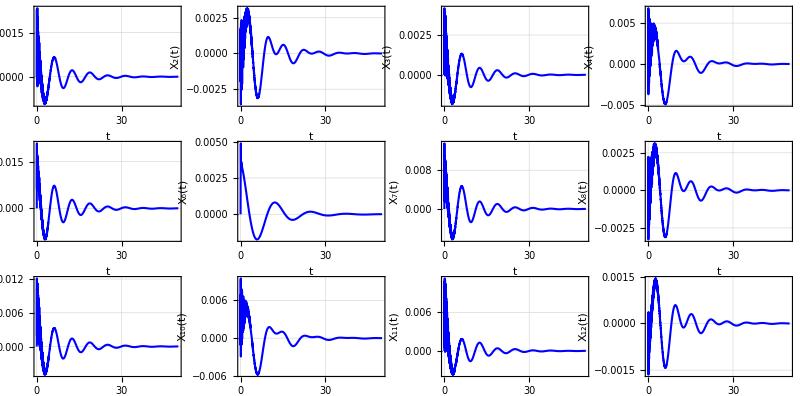

```mathematica
(* Initialization for a vector to store the modal DOF solutions. *)
ModalDOFSolutions = ConstantArray[0,Dimensions[EigVectors]];

(* Solve each uncoupled differential equation for the modal DOF solution. *)
For[i=1, i<=Length[EigValues], i++,
temp = DSolve[{q''[t]+2*DampingRatios[[i]]*NaturalFrequencies[[i]]*q'[t]+NaturalFrequencies[[i]]^2*q[t]==Fmodal[[i]],q[0]==0,q'[0]==0},q[t],t][[1]];
temp = Chop[ComplexExpand[Re[Chop[TrigReduce[Chop[TrigExpand[Chop[FullSimplify[Chop[ComplexExpand[Re[temp]]]]]]]]]]]];
ModalDOFSolutions[[i]] = q[t]/.temp;
]

(* Show the modal DOF solutions and plot the results. *)
Print[Style["Solutions of uncoupled differential equations q(t) (modal DOF solutions):", Bold, FontFamily->"Times", FontSize->14]]
Magnify[MatrixForm[ModalDOFSolutions], 0.625]

Print[Style["Plot for modal DOF solutions q(t):", Bold, FontFamily->"Times", FontSize->14]]
Plots = Table[Plot[ModalDOFSolutions[[i]], {t, 0, 50}, ImageSize->{300, 200}, PlotStyle->{Directive[Blue, AbsoluteThickness[1.5]]},FrameLabel->{Style["t"], Style[Row[{Subscript["q",ToString[i]],"(t)"}]]}, GridLines->Automatic, LabelStyle->{RGBColor[0,0,0], Bold, FontSize->9, FontFamily->"Times"}, PlotRange->All, Frame->True],{i,1,12}];
GraphicsGrid[Partition[Plots,4],ImageSize->800]

(* Calculate the spatial DOF solutions. *)
Xspatial = Dot[MassNormalizedModes,ModalDOFSolutions];
Print[Style["Spatial DOF solutions:", Bold, FontFamily->"Times", FontSize->14]]

Print[Style["X1(t) =", Bold, FontFamily->"Times", FontSize->14]]
Xspatial[[1]]
Print[Style["X2(t) =", Bold, FontFamily->"Times", FontSize->14]]
Xspatial[[2]]
Print[Style["X3(t) =", Bold, FontFamily->"Times", FontSize->14]]
Xspatial[[3]]
Print[Style["X4(t) =", Bold, FontFamily->"Times", FontSize->14]]
Xspatial[[4]]
Print[Style["X5(t) =", Bold, FontFamily->"Times", FontSize->14]]
Xspatial[[5]]
Print[Style["X6(t) =", Bold, FontFamily->"Times", FontSize->14]]
Xspatial[[6]]
Print[Style["X7(t) =", Bold, FontFamily->"Times", FontSize->14]]
Xspatial[[7]]
Print[Style["X8(t) =", Bold, FontFamily->"Times", FontSize->14]]
Xspatial[[8]]
Print[Style["X9(t) =", Bold, FontFamily->"Times", FontSize->14]]
Xspatial[[9]]
Print[Style["X10(t) =", Bold, FontFamily->"Times", FontSize->14]]
Xspatial[[10]]
Print[Style["X11(t) =", Bold, FontFamily->"Times", FontSize->14]]
Xspatial[[11]]
Print[Style["X12(t) =", Bold, FontFamily->"Times", FontSize->14]]
Xspatial[[12]]

(* Plot the spatial DOF solutions. *)
Print[Style["Plot for spatial DOF solutions X(t):", Bold, FontFamily->"Times", FontSize->14]]
Plots = Table[Plot[Xspatial[[i]], {t, 0, 50}, ImageSize->{300, 200}, PlotStyle->{Directive[Blue, AbsoluteThickness[1.5]]},FrameLabel->{Style["t"], Style[Row[{Subscript["X",ToString[i]],"(t)"}]]}, GridLines->Automatic, LabelStyle->{RGBColor[0,0,0], Bold, FontSize->9, FontFamily->"Times"}, PlotRange->All, Frame->True],{i,1,12}];
GraphicsGrid[Partition[Plots,4],ImageSize->800]
```

## Problem 12

Fourier transform of the input force vector:

(0
0
0
0
ConditionalExpression[3651.84/(1.02901-1.9712 Ω^2+1. Ω^4)+(Ω ((0.+29568. ⅈ)+(3600.-(0.+30000. ⅈ) Ω) Ω))/(1.02901-1.9712 Ω^2+1. Ω^4), Re[(0.-1. ⅈ) Ω]<0.12&&Re[(0.+1. ⅈ) Ω]>-0.12]
ConditionalExpression[634.56/(0.0699074-0.4712 Ω^2+1. Ω^4)+(Ω ((0.+4712. ⅈ)+(2400.-(0.+20000. ⅈ) Ω) Ω))/(0.0699074-0.4712 Ω^2+1. Ω^4), Re[(0.-1. ⅈ) Ω]<0.12&&Re[(0.+1. ⅈ) Ω]>-0.12]
0
0
0
ConditionalExpression[317.28/(0.0699074-0.4712 Ω^2+1. Ω^4)+(Ω ((0.+2356. ⅈ)+(1200.-(0.+10000. ⅈ) Ω) Ω))/(0.0699074-0.4712 Ω^2+1. Ω^4), Re[(0.-1. ⅈ) Ω]<0.12&&Re[(0.+1. ⅈ) Ω]>-0.12]
0
0)

Magnitude plot for the Fourier transform of the input force vector F(Ω):

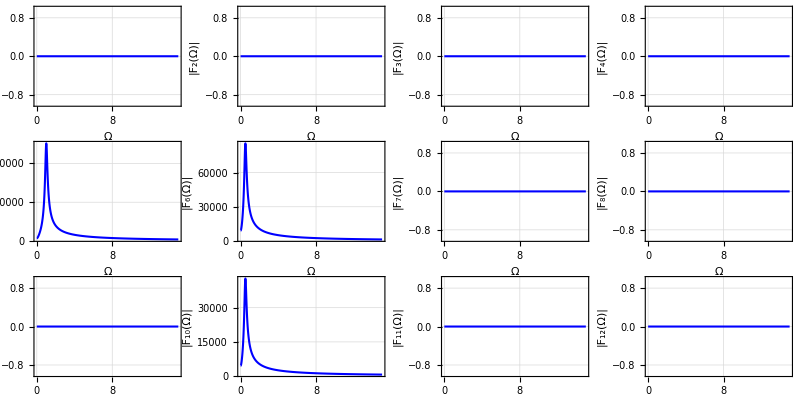

Phase plot for the Fourier transform of the input force vector F(Ω):

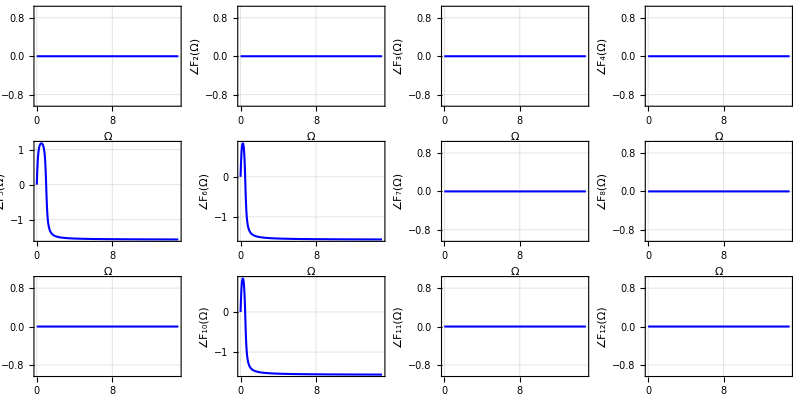

Closed form analytical solution of the Fourier transform X(Ω) of output displacements X(t):

(ConditionalExpression[(7.40312×10^68+Ω ((0.+6.87613×10^69 ⅈ)+Ω (-1.42743×10^70+Ω ((1.83899×10^55-6.88828×10^70 ⅈ)+Ω (2.40461×10^70+Ω ((7.35598×10^55+2.62794×10^71 ⅈ)+Ω (2.38287×10^70+Ω ((3.67799×10^55-2.01086×10^71 ⅈ)+Ω (2.20751×10^68+Ω ((2.24487×10^51+3.39966×10^67 ⅈ)+Ω (-3.19583×10^64+Ω ((-4.56719×10^46-1.12877×10^63 ⅈ)+Ω (9.12842×10^59+Ω ((-3.48449×10^41+9.04181×10^57 ⅈ)+Ω (-6.09937×10^54+Ω ((0.+2.38081×10^52 ⅈ)+Ω (-1.63924×10^49+Ω ((0.-3.96368×10^47 ⅈ)+Ω (1.9772×10^44+Ω ((0.+3.16826×10^41 ⅈ)+Ω (-9.57097×10^37+Ω ((0.+3.99245×10^36 ⅈ)+Ω (-1.23202×10^33+Ω ((0.-5.87488×10^30 ⅈ)+Ω (1.07954×10^27+Ω ((0.-1.2004×10^25 ⅈ)+(1.34495×10^21+(0.+2.02887×10^19 ⅈ) Ω) Ω))))))))))))))))))))))))))/((1.02901-1.9712 Ω^2+1. Ω^4) (0.0699074-0.4712 Ω^2+1. Ω^4) (2.02674×10^74+Ω ((0.+2.64074×10^71 ⅈ)+Ω (-5.89177×10^70+Ω ((0.-6.69052×10^67 ⅈ)+Ω (5.81151×10^66+Ω ((0.+5.73541×10^63 ⅈ)+Ω (-2.52748×10^62+Ω ((0.-2.16336×10^59 ⅈ)+Ω (5.61992×10^57+Ω ((0.+4.13647×10^54 ⅈ)+Ω (-7.04564×10^52+Ω ((0.-4.38791×10^49 ⅈ)+Ω (5.2617×10^47+Ω ((0.+2.7046×10^44 ⅈ)+Ω (-2.40621×10^42+Ω ((0.-9.82836×10^38 ⅈ)+Ω (6.75921×10^36+Ω ((0.+2.06253×10^33 ⅈ)+Ω (-1.13216×10^31+Ω ((0.-2.30061×10^27 ⅈ)+Ω (1.03333×10^25+((0.+1.05184×10^21 ⅈ)-3.94133×10^18 Ω) Ω)))))))))))))))))))))), Re[(0.-1. ⅈ) Ω]<0.12&&Re[(0.+1. ⅈ) Ω]>-0.12]
ConditionalExpression[(1.49507×10^70+Ω ((0.+1.0713×10^71 ⅈ)+Ω (7.21221×10^70+Ω ((1.96159×10^56-5.84649×10^71 ⅈ)+Ω (-1.74216×10^71+Ω ((2.45199×10^55+4.07766×10^71 ⅈ)+Ω (-6.14416×10^69+Ω ((1.5325×10^54+4.74261×10^70 ⅈ)+Ω (-3.81059×10^67+Ω ((3.3673×10^51+1.60719×10^67 ⅈ)+Ω (-1.60004×10^64+Ω ((-4.56719×10^46-1.19974×10^63 ⅈ)+Ω (9.8505×10^59+Ω ((-2.78759×10^42+1.50493×10^58 ⅈ)+Ω (-1.03496×10^55+Ω ((0.+5.02138×10^50 ⅈ)+Ω (-3.72617×10^48+Ω ((0.-6.18472×10^47 ⅈ)+Ω (3.13698×10^44+Ω ((0.+1.27723×10^42 ⅈ)+Ω (-4.61265×10^38+Ω ((0.+6.34266×10^36 ⅈ)+Ω (-1.99869×10^33+Ω ((0.-1.49294×10^31 ⅈ)+Ω (2.82744×10^27+Ω ((0.-1.99379×10^25 ⅈ)+(2.3132×10^21+(0.+4.44812×10^19 ⅈ) Ω) Ω))))))))))))))))))))))))))/((1.02901-1.9712 Ω^2+1. Ω^4) (0.0699074-0.4712 Ω^2+1. Ω^4) (2.02674×10^74+Ω ((0.+2.64074×10^71 ⅈ)+Ω (-5.89177×10^70+Ω ((0.-6.69052×10^67 ⅈ)+Ω (5.81151×10^66+Ω ((0.+5.73541×10^63 ⅈ)+Ω (-2.52748×10^62+Ω ((0.-2.16336×10^59 ⅈ)+Ω (5.61992×10^57+Ω ((0.+4.13647×10^54 ⅈ)+Ω (-7.04564×10^52+Ω ((0.-4.38791×10^49 ⅈ)+Ω (5.2617×10^47+Ω ((0.+2.7046×10^44 ⅈ)+Ω (-2.40621×10^42+Ω ((0.-9.82836×10^38 ⅈ)+Ω (6.75921×10^36+Ω ((0.+2.06253×10^33 ⅈ)+Ω (-1.13216×10^31+Ω ((0.-2.30061×10^27 ⅈ)+Ω (1.03333×10^25+((0.+1.05184×10^21 ⅈ)-3.94133×10^18 Ω) Ω)))))))))))))))))))))), Re[(0.-1. ⅈ) Ω]<0.12&&Re[(0.+1. ⅈ) Ω]>-0.12]
ConditionalExpression[(1.48062×10^69+Ω ((0.+1.37523×10^70 ⅈ)+Ω (-2.85487×10^70+Ω ((2.45199×10^55-1.37766×10^71 ⅈ)+Ω (4.80931×10^70+Ω ((0.+5.2559×10^71 ⅈ)+Ω (4.76541×10^70+Ω ((4.90399×10^55-4.02177×10^71 ⅈ)+Ω (4.43307×10^68+Ω ((-1.19726×10^52+7.10978×10^67 ⅈ)+Ω (-6.73894×10^64+Ω ((0.-2.79005×10^63 ⅈ)+Ω (2.28758×10^60+Ω ((-7.66588×10^42+3.68327×10^58 ⅈ)+Ω (-2.57268×10^55+Ω ((0.-1.38835×10^53 ⅈ)+Ω (7.75395×10^49+Ω ((0.-6.91625×10^47 ⅈ)+Ω (3.78871×10^44+Ω ((0.+6.4928×10^42 ⅈ)+Ω (-2.62741×10^39+Ω ((0.-1.17315×10^37 ⅈ)+Ω (3.29733×10^33+Ω ((0.-2.32274×10^31 ⅈ)+Ω (5.28876×10^27+Ω ((0.+9.58511×10^25 ⅈ)+(-1.01138×10^22-(0.+8.11549×10^19 ⅈ) Ω) Ω))))))))))))))))))))))))))/((1.02901-1.9712 Ω^2+1. Ω^4) (0.0699074-0.4712 Ω^2+1. Ω^4) (2.02674×10^74+Ω ((0.+2.64074×10^71 ⅈ)+Ω (-5.89177×10^70+Ω ((0.-6.69052×10^67 ⅈ)+Ω (5.81151×10^66+Ω ((0.+5.73541×10^63 ⅈ)+Ω (-2.52748×10^62+Ω ((0.-2.16336×10^59 ⅈ)+Ω (5.61992×10^57+Ω ((0.+4.13647×10^54 ⅈ)+Ω (-7.04564×10^52+Ω ((0.-4.38791×10^49 ⅈ)+Ω (5.2617×10^47+Ω ((0.+2.7046×10^44 ⅈ)+Ω (-2.40621×10^42+Ω ((0.-9.82836×10^38 ⅈ)+Ω (6.75921×10^36+Ω ((0.+2.06253×10^33 ⅈ)+Ω (-1.13216×10^31+Ω ((0.-2.30061×10^27 ⅈ)+Ω (1.03333×10^25+((0.+1.05184×10^21 ⅈ)-3.94133×10^18 Ω) Ω)))))))))))))))))))))), Re[(0.-1. ⅈ) Ω]<0.12&&Re[(0.+1. ⅈ) Ω]>-0.12]
ConditionalExpression[(3.1382×10^70+Ω ((0.+2.28013×10^71 ⅈ)+Ω (1.15687×10^71+Ω ((2.94239×10^56-1.30707×10^72 ⅈ)+Ω (-3.00309×10^71+Ω ((1.4712×10^56+1.34116×10^72 ⅈ)+Ω (3.53558×10^70+Ω ((-1.226×10^55-3.07362×10^71 ⅈ)+Ω (3.64659×10^68+Ω ((-2.69384×10^52+9.89751×10^67 ⅈ)+Ω (-9.73519×10^64+Ω ((-2.55763×10^48-6.59663×10^63 ⅈ)+Ω (5.62183×10^60+Ω ((-3.90263×10^43+1.87841×10^59 ⅈ)+Ω (-1.37211×10^56+Ω ((0.-2.55977×10^54 ⅈ)+Ω (1.57358×10^51+Ω ((0.+1.6997×10^49 ⅈ)+Ω (-8.54114×10^45+Ω ((0.-4.82743×10^43 ⅈ)+Ω (1.87477×10^40+Ω ((0.-6.37168×10^36 ⅈ)+Ω (4.47852×10^33+Ω ((0.+3.50324×10^32 ⅈ)+Ω (-7.44009×10^28+Ω ((0.-7.22361×10^26 ⅈ)+(7.50293×10^22+(0.+4.63412×10^20 ⅈ) Ω) Ω))))))))))))))))))))))))))/((1.02901-1.9712 Ω^2+1. Ω^4) (0.0699074-0.4712 Ω^2+1. Ω^4) (2.02674×10^74+Ω ((0.+2.64074×10^71 ⅈ)+Ω (-5.89177×10^70+Ω ((0.-6.69052×10^67 ⅈ)+Ω (5.81151×10^66+Ω ((0.+5.73541×10^63 ⅈ)+Ω (-2.52748×10^62+Ω ((0.-2.16336×10^59 ⅈ)+Ω (5.61992×10^57+Ω ((0.+4.13647×10^54 ⅈ)+Ω (-7.04564×10^52+Ω ((0.-4.38791×10^49 ⅈ)+Ω (5.2617×10^47+Ω ((0.+2.7046×10^44 ⅈ)+Ω (-2.40621×10^42+Ω ((0.-9.82836×10^38 ⅈ)+Ω (6.75921×10^36+Ω ((0.+2.06253×10^33 ⅈ)+Ω (-1.13216×10^31+Ω ((0.-2.30061×10^27 ⅈ)+Ω (1.03333×10^25+((0.+1.05184×10^21 ⅈ)-3.94133×10^18 Ω) Ω)))))))))))))))))))))), Re[(0.-1. ⅈ) Ω]<0.12&&Re[(0.+1. ⅈ) Ω]>-0.12]
ConditionalExpression[(1.41399×10^70+Ω ((0.+1.20966×10^71 ⅈ)+Ω (-1.54894×10^71+Ω ((1.96159×10^56-1.05219×10^72 ⅈ)+Ω (2.43746×10^71+Ω ((3.92319×10^56+3.41867×10^72 ⅈ)+Ω (2.95723×10^71+Ω ((7.84638×10^56-2.49863×10^72 ⅈ)+Ω (2.84187×10^69+Ω ((2.39452×10^52+5.93009×10^68 ⅈ)+Ω (-5.89854×10^65+Ω ((-4.3845×10^48-4.48052×10^64 ⅈ)+Ω (3.86904×10^61+Ω ((8.9203×10^43+1.52363×10^60 ⅈ)+Ω (-1.1297×10^57+Ω ((0.-2.65733×10^55 ⅈ)+Ω (1.66507×10^52+Ω ((0.+2.58564×10^50 ⅈ)+Ω (-1.33606×10^47+Ω ((0.-1.47367×10^45 ⅈ)+Ω (6.04644×10^41+Ω ((0.+4.99242×10^39 ⅈ)+Ω (-1.52903×10^36+Ω ((0.-9.83073×10^33 ⅈ)+Ω (2.00327×10^30+Ω ((0.+1.03398×10^28 ⅈ)+(-1.05445×10^24-(0.+4.47515×10^21 ⅈ) Ω) Ω))))))))))))))))))))))))))/((1.02901-1.9712 Ω^2+1. Ω^4) (0.0699074-0.4712 Ω^2+1. Ω^4) (2.02674×10^74+Ω ((0.+2.64074×10^71 ⅈ)+Ω (-5.89177×10^70+Ω ((0.-6.69052×10^67 ⅈ)+Ω (5.81151×10^66+Ω ((0.+5.73541×10^63 ⅈ)+Ω (-2.52748×10^62+Ω ((0.-2.16336×10^59 ⅈ)+Ω (5.61992×10^57+Ω ((0.+4.13647×10^54 ⅈ)+Ω (-7.04564×10^52+Ω ((0.-4.38791×10^49 ⅈ)+Ω (5.2617×10^47+Ω ((0.+2.7046×10^44 ⅈ)+Ω (-2.40621×10^42+Ω ((0.-9.82836×10^38 ⅈ)+Ω (6.75921×10^36+Ω ((0.+2.06253×10^33 ⅈ)+Ω (-1.13216×10^31+Ω ((0.-2.30061×10^27 ⅈ)+Ω (1.03333×10^25+((0.+1.05184×10^21 ⅈ)-3.94133×10^18 Ω) Ω)))))))))))))))))))))), Re[(0.-1. ⅈ) Ω]<0.12&&Re[(0.+1. ⅈ) Ω]>-0.12]
ConditionalExpression[(-22.0333+Ω ((0.-163.611 ⅈ)+(-83.3333+(0.+694.444 ⅈ) Ω) Ω))/((0.0699074-0.4712 Ω^2+1. Ω^4) (-194444.+Ω ((0.-20.1444 ⅈ)+1. Ω))), Re[(0.-1. ⅈ) Ω]<0.12&&Re[(0.+1. ⅈ) Ω]>-0.12]
ConditionalExpression[(4.90054×10^69+Ω ((0.+4.6146×10^70 ⅈ)+Ω (-1.01633×10^71+Ω ((1.7164×10^56-4.71961×10^71 ⅈ)+Ω (1.72264×10^71+Ω ((3.92319×10^56+1.8367×10^72 ⅈ)+Ω (1.67339×10^71+Ω ((-3.92319×10^56-1.41259×10^72 ⅈ)+Ω (1.58273×10^69+Ω ((-7.18751×10^52+2.93998×10^68 ⅈ)+Ω (-2.86374×10^65+Ω ((7.30751×10^47-1.75126×10^64 ⅈ)+Ω (1.48178×10^61+Ω ((7.80526×10^43+4.4773×10^59 ⅈ)+Ω (-3.25303×10^56+Ω ((0.-5.54086×10^54 ⅈ)+Ω (3.39121×10^51+Ω ((0.+3.3445×10^49 ⅈ)+Ω (-1.67308×10^46+Ω ((0.-8.30121×10^43 ⅈ)+Ω (3.19516×10^40+Ω ((0.-4.55694×10^37 ⅈ)+Ω (1.83781×10^34+Ω ((0.+6.59744×10^32 ⅈ)+Ω (-1.39128×10^29+Ω ((0.-1.2273×10^27 ⅈ)+(1.27081×10^23+(0.+7.39202×10^20 ⅈ) Ω) Ω))))))))))))))))))))))))))/((1.02901-1.9712 Ω^2+1. Ω^4) (0.0699074-0.4712 Ω^2+1. Ω^4) (2.02674×10^74+Ω ((0.+2.64074×10^71 ⅈ)+Ω (-5.89177×10^70+Ω ((0.-6.69052×10^67 ⅈ)+Ω (5.81151×10^66+Ω ((0.+5.73541×10^63 ⅈ)+Ω (-2.52748×10^62+Ω ((0.-2.16336×10^59 ⅈ)+Ω (5.61992×10^57+Ω ((0.+4.13647×10^54 ⅈ)+Ω (-7.04564×10^52+Ω ((0.-4.38791×10^49 ⅈ)+Ω (5.2617×10^47+Ω ((0.+2.7046×10^44 ⅈ)+Ω (-2.40621×10^42+Ω ((0.-9.82836×10^38 ⅈ)+Ω (6.75921×10^36+Ω ((0.+2.06253×10^33 ⅈ)+Ω (-1.13216×10^31+Ω ((0.-2.30061×10^27 ⅈ)+Ω (1.03333×10^25+((0.+1.05184×10^21 ⅈ)-3.94133×10^18 Ω) Ω)))))))))))))))))))))), Re[(0.-1. ⅈ) Ω]<0.12&&Re[(0.+1. ⅈ) Ω]>-0.12]
ConditionalExpression[(1.49507×10^70+Ω ((0.+1.0713×10^71 ⅈ)+Ω (7.21214×10^70+Ω ((2.45199×10^56-5.8465×10^71 ⅈ)+Ω (-1.74214×10^71+Ω ((0.+4.0777×10^71 ⅈ)+Ω (-6.14502×10^69+Ω ((3.06499×10^54+4.74229×10^70 ⅈ)+Ω (-3.83149×10^67+Ω ((0.+1.57059×10^67 ⅈ)+Ω (-1.58286×10^64+Ω ((-1.1418×10^47-1.32288×10^63 ⅈ)+Ω (1.10243×10^60+Ω ((-6.96898×10^41+2.46149×10^58 ⅈ)+Ω (-1.73923×10^55+Ω ((0.-1.39554×10^53 ⅈ)+Ω (8.04672×10^49+Ω ((0.-2.70489×10^47 ⅈ)+Ω (1.63457×10^44+Ω ((0.+5.16993×10^42 ⅈ)+Ω (-2.11952×10^39+Ω ((0.-1.33597×10^37 ⅈ)+Ω (3.85471×10^33+Ω ((0.-1.37808×10^31 ⅈ)+Ω (3.38774×10^27+Ω ((0.+9.22386×10^25 ⅈ)+(-9.81587×10^21-(0.+8.89624×10^19 ⅈ) Ω) Ω))))))))))))))))))))))))))/((1.02901-1.9712 Ω^2+1. Ω^4) (0.0699074-0.4712 Ω^2+1. Ω^4) (2.02674×10^74+Ω ((0.+2.64074×10^71 ⅈ)+Ω (-5.89177×10^70+Ω ((0.-6.69052×10^67 ⅈ)+Ω (5.81151×10^66+Ω ((0.+5.73541×10^63 ⅈ)+Ω (-2.52748×10^62+Ω ((0.-2.16336×10^59 ⅈ)+Ω (5.61992×10^57+Ω ((0.+4.13647×10^54 ⅈ)+Ω (-7.04564×10^52+Ω ((0.-4.38791×10^49 ⅈ)+Ω (5.2617×10^47+Ω ((0.+2.7046×10^44 ⅈ)+Ω (-2.40621×10^42+Ω ((0.-9.82836×10^38 ⅈ)+Ω (6.75921×10^36+Ω ((0.+2.06253×10^33 ⅈ)+Ω (-1.13216×10^31+Ω ((0.-2.30061×10^27 ⅈ)+Ω (1.03333×10^25+((0.+1.05184×10^21 ⅈ)-3.94133×10^18 Ω) Ω)))))))))))))))))))))), Re[(0.-1. ⅈ) Ω]<0.12&&Re[(0.+1. ⅈ) Ω]>-0.12]
ConditionalExpression[(9.69807×10^69+Ω ((0.+7.97088×10^70 ⅈ)+Ω (-6.92432×10^70+Ω ((1.96159×10^56-6.38877×10^71 ⅈ)+Ω (9.94236×10^70+Ω ((0.+1.84184×10^72 ⅈ)+Ω (1.52898×10^71+Ω ((1.4712×10^56-1.29193×10^72 ⅈ)+Ω (1.43512×10^69+Ω ((4.19042×10^52+2.47479×10^68 ⅈ)+Ω (-2.36534×10^65+Ω ((-2.19225×10^48-1.12229×10^64 ⅈ)+Ω (9.2845×10^60+Ω ((-7.5265×10^43+1.86061×10^59 ⅈ)+Ω (-1.3179×10^56+Ω ((0.-1.23775×10^54 ⅈ)+Ω (7.31226×10^50+Ω ((0.+1.93613×10^48 ⅈ)+Ω (-8.4816×10^44+Ω ((0.+1.28008×10^43 ⅈ)+Ω (-5.39568×10^39+Ω ((0.-4.84312×10^37 ⅈ)+Ω (1.43242×10^34+Ω ((0.-4.46663×10^29 ⅈ)+Ω (1.46685×10^27+Ω ((0.+1.8459×10^26 ⅈ)+(-1.97344×10^22-(0.+1.87366×10^20 ⅈ) Ω) Ω))))))))))))))))))))))))))/((1.02901-1.9712 Ω^2+1. Ω^4) (0.0699074-0.4712 Ω^2+1. Ω^4) (2.02674×10^74+Ω ((0.+2.64074×10^71 ⅈ)+Ω (-5.89177×10^70+Ω ((0.-6.69052×10^67 ⅈ)+Ω (5.81151×10^66+Ω ((0.+5.73541×10^63 ⅈ)+Ω (-2.52748×10^62+Ω ((0.-2.16336×10^59 ⅈ)+Ω (5.61992×10^57+Ω ((0.+4.13647×10^54 ⅈ)+Ω (-7.04564×10^52+Ω ((0.-4.38791×10^49 ⅈ)+Ω (5.2617×10^47+Ω ((0.+2.7046×10^44 ⅈ)+Ω (-2.40621×10^42+Ω ((0.-9.82836×10^38 ⅈ)+Ω (6.75921×10^36+Ω ((0.+2.06253×10^33 ⅈ)+Ω (-1.13216×10^31+Ω ((0.-2.30061×10^27 ⅈ)+Ω (1.03333×10^25+((0.+1.05184×10^21 ⅈ)-3.94133×10^18 Ω) Ω)))))))))))))))))))))), Re[(0.-1. ⅈ) Ω]<0.12&&Re[(0.+1. ⅈ) Ω]>-0.12]
ConditionalExpression[(4.3198×10^70+Ω ((0.+3.15768×10^71 ⅈ)+Ω (1.37635×10^71+Ω ((8.82717×10^56-1.84756×10^72 ⅈ)+Ω (-3.738×10^71+Ω ((1.96159×10^56+2.1399×10^72 ⅈ)+Ω (7.78538×10^70+Ω ((2.66612×10^56-6.69444×10^71 ⅈ)+Ω (7.85176×10^68+Ω ((-2.99316×10^52+1.99915×10^68 ⅈ)+Ω (-1.99635×10^65+Ω ((1.82688×10^48-1.56803×10^64 ⅈ)+Ω (1.35566×10^61+Ω ((4.46015×10^43+5.40696×10^59 ⅈ)+Ω (-4.00591×10^56+Ω ((0.-9.30296×10^54 ⅈ)+Ω (5.81979×10^51+Ω ((0.+8.79302×10^49 ⅈ)+Ω (-4.53678×10^46+Ω ((0.-4.88035×10^44 ⅈ)+Ω (2.00097×10^41+Ω ((0.+1.63733×10^39 ⅈ)+Ω (-5.01615×10^35+Ω ((0.-3.26273×10^33 ⅈ)+Ω (6.65628×10^29+Ω ((0.+3.53911×10^27 ⅈ)+(-3.6149×10^23-(0.+1.60022×10^21 ⅈ) Ω) Ω))))))))))))))))))))))))))/((1.02901-1.9712 Ω^2+1. Ω^4) (0.0699074-0.4712 Ω^2+1. Ω^4) (2.02674×10^74+Ω ((0.+2.64074×10^71 ⅈ)+Ω (-5.89177×10^70+Ω ((0.-6.69052×10^67 ⅈ)+Ω (5.81151×10^66+Ω ((0.+5.73541×10^63 ⅈ)+Ω (-2.52748×10^62+Ω ((0.-2.16336×10^59 ⅈ)+Ω (5.61992×10^57+Ω ((0.+4.13647×10^54 ⅈ)+Ω (-7.04564×10^52+Ω ((0.-4.38791×10^49 ⅈ)+Ω (5.2617×10^47+Ω ((0.+2.7046×10^44 ⅈ)+Ω (-2.40621×10^42+Ω ((0.-9.82836×10^38 ⅈ)+Ω (6.75921×10^36+Ω ((0.+2.06253×10^33 ⅈ)+Ω (-1.13216×10^31+Ω ((0.-2.30061×10^27 ⅈ)+Ω (1.03333×10^25+((0.+1.05184×10^21 ⅈ)-3.94133×10^18 Ω) Ω)))))))))))))))))))))), Re[(0.-1. ⅈ) Ω]<0.12&&Re[(0.+1. ⅈ) Ω]>-0.12]
ConditionalExpression[(1.44956×10^70+Ω ((0.+1.13272×10^71 ⅈ)+Ω (-3.68545×10^70+Ω ((1.4712×10^56-8.05795×10^71 ⅈ)+Ω (2.65908×10^70+Ω ((6.86558×10^56+1.84699×10^72 ⅈ)+Ω (1.38436×10^71+Ω ((-2.94239×10^56-1.1713×10^72 ⅈ)+Ω (1.2991×10^69+Ω ((5.98631×10^51+2.20908×10^68 ⅈ)+Ω (-2.09579×10^65+Ω ((0.-8.80302×10^63 ⅈ)+Ω (7.20065×10^60+Ω ((1.95132×10^43+1.07257×10^59 ⅈ)+Ω (-7.44462×10^55+Ω ((0.-2.63562×10^53 ⅈ)+Ω (1.41195×10^50+Ω ((0.-2.11137×10^48 ⅈ)+Ω (1.10578×10^45+Ω ((0.+9.48558×10^42 ⅈ)+Ω (-3.71299×10^39+Ω ((0.+2.21916×10^36 ⅈ)+Ω (-1.06668×10^33+Ω ((0.-4.97485×10^31 ⅈ)+Ω (1.02056×10^28+Ω ((0.+4.54801×10^25 ⅈ)+(-4.42503×10^21+(0.+1.02637×10^19 ⅈ) Ω) Ω))))))))))))))))))))))))))/((1.02901-1.9712 Ω^2+1. Ω^4) (0.0699074-0.4712 Ω^2+1. Ω^4) (2.02674×10^74+Ω ((0.+2.64074×10^71 ⅈ)+Ω (-5.89177×10^70+Ω ((0.-6.69052×10^67 ⅈ)+Ω (5.81151×10^66+Ω ((0.+5.73541×10^63 ⅈ)+Ω (-2.52748×10^62+Ω ((0.-2.16336×10^59 ⅈ)+Ω (5.61992×10^57+Ω ((0.+4.13647×10^54 ⅈ)+Ω (-7.04564×10^52+Ω ((0.-4.38791×10^49 ⅈ)+Ω (5.2617×10^47+Ω ((0.+2.7046×10^44 ⅈ)+Ω (-2.40621×10^42+Ω ((0.-9.82836×10^38 ⅈ)+Ω (6.75921×10^36+Ω ((0.+2.06253×10^33 ⅈ)+Ω (-1.13216×10^31+Ω ((0.-2.30061×10^27 ⅈ)+Ω (1.03333×10^25+((0.+1.05184×10^21 ⅈ)-3.94133×10^18 Ω) Ω)))))))))))))))))))))), Re[(0.-1. ⅈ) Ω]<0.12&&Re[(0.+1. ⅈ) Ω]>-0.12]
ConditionalExpression[(4.79753×10^69+Ω ((0.+3.3563×10^70 ⅈ)+Ω (3.23882×10^70+Ω ((6.12998×10^55-1.66919×10^71 ⅈ)+Ω (-7.28289×10^70+Ω ((5.74686×10^53+5.15654×10^69 ⅈ)+Ω (-1.4473×10^70+Ω ((2.45199×10^55+1.20621×10^71 ⅈ)+Ω (-1.30219×10^68+Ω ((-4.48973×10^51-1.65983×10^67 ⅈ)+Ω (1.56107×10^64+Ω ((1.82688×10^47+5.61944×10^62 ⅈ)+Ω (-4.49376×10^59+Ω ((-4.35561×10^40-1.90114×10^57 ⅈ)+Ω (1.08901×10^54+Ω ((0.-6.05294×10^52 ⅈ)+Ω (3.6813×10^49+Ω ((0.+1.18452×10^47 ⅈ)+Ω (-4.20347×10^43+Ω ((0.+3.37605×10^42 ⅈ)+Ω (-1.4153×10^39+Ω ((0.-1.33945×10^37 ⅈ)+Ω (3.92685×10^33+Ω ((0.-6.98754×10^30 ⅈ)+Ω (1.97215×10^27+Ω ((0.+8.26611×10^25 ⅈ)+(-8.82736×10^21-(0.+8.34195×10^19 ⅈ) Ω) Ω))))))))))))))))))))))))))/((1.02901-1.9712 Ω^2+1. Ω^4) (0.0699074-0.4712 Ω^2+1. Ω^4) (2.02674×10^74+Ω ((0.+2.64074×10^71 ⅈ)+Ω (-5.89177×10^70+Ω ((0.-6.69052×10^67 ⅈ)+Ω (5.81151×10^66+Ω ((0.+5.73541×10^63 ⅈ)+Ω (-2.52748×10^62+Ω ((0.-2.16336×10^59 ⅈ)+Ω (5.61992×10^57+Ω ((0.+4.13647×10^54 ⅈ)+Ω (-7.04564×10^52+Ω ((0.-4.38791×10^49 ⅈ)+Ω (5.2617×10^47+Ω ((0.+2.7046×10^44 ⅈ)+Ω (-2.40621×10^42+Ω ((0.-9.82836×10^38 ⅈ)+Ω (6.75921×10^36+Ω ((0.+2.06253×10^33 ⅈ)+Ω (-1.13216×10^31+Ω ((0.-2.30061×10^27 ⅈ)+Ω (1.03333×10^25+((0.+1.05184×10^21 ⅈ)-3.94133×10^18 Ω) Ω)))))))))))))))))))))), Re[(0.-1. ⅈ) Ω]<0.12&&Re[(0.+1. ⅈ) Ω]>-0.12])

Magnitude plot for the Fourier transform of the output displacement vector X(Ω):

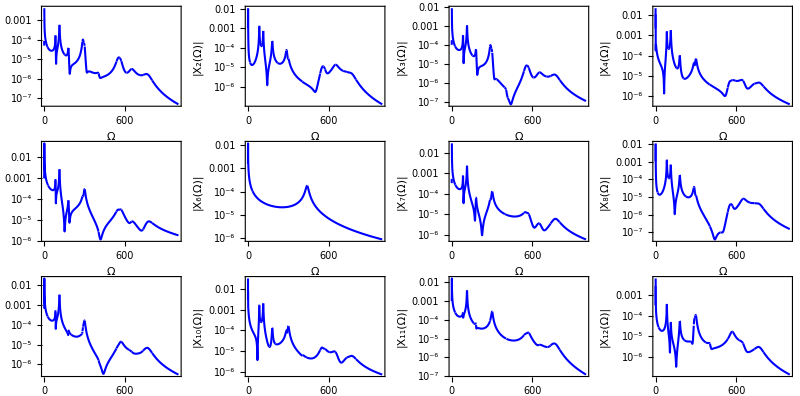

Phase plot for the Fourier transform of the output displacement vector X(Ω):

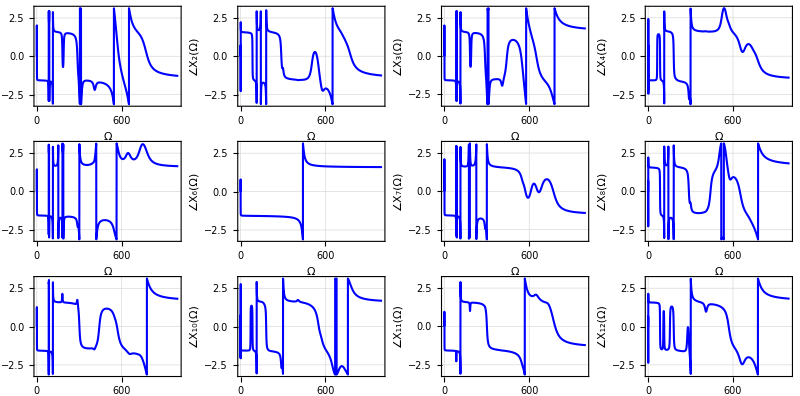

```mathematica
(* Calculate the Fourier transform of the input force vector. *)
Print[Style["Fourier transform of the input force vector:", Bold, FontFamily->"Times", FontSize->14]]
Ffrequency= Integrate[Fsystem*Exp[-I*Ω*t], {t, 0,Infinity}];
Ffrequency = Chop[FullSimplify[ComplexExpand[Ffrequency]]];
MatrixForm[Ffrequency]

(* Plot the magnitude for the Fourier transform of the input force vector. *)
Print[Style["Magnitude plot for the Fourier transform of the input force vector F(Ω):", Bold, FontFamily->"Times", FontSize->14]]
Plots = Table[Plot[Abs[Ffrequency[[i]]], {Ω, 0, 15}, ImageSize->{300, 200}, PlotStyle->{Directive[Blue, AbsoluteThickness[1.5]]},FrameLabel->{Style["Ω"], Style[Row[{"|",Subscript["F",ToString[i]],"(Ω)|"}]]}, GridLines->Automatic, LabelStyle->{RGBColor[0,0,0], Bold, FontSize->9, FontFamily->"Times"}, PlotRange->All, Frame->True],{i,1,12}];
GraphicsGrid[Partition[Plots,4],ImageSize->800]

(* Plot the phase for the Fourier transform of the input force vector. *)
Print[Style["Phase plot for the Fourier transform of the input force vector F(Ω):", Bold, FontFamily->"Times", FontSize->14]]
Plots = Table[Plot[FullSimplify[Arg[Ffrequency[[i]]]], {Ω, 0, 15}, ImageSize->{300, 200}, PlotStyle->{Directive[Blue, AbsoluteThickness[1.5]]},FrameLabel->{Style["Ω"], Style[Row[{"∠",Subscript["F",ToString[i]],"(Ω)"}]]}, GridLines->Automatic, LabelStyle->{RGBColor[0,0,0], Bold, FontSize->9, FontFamily->"Times"}, PlotRange->All, Frame->True],{i,1,12}];
GraphicsGrid[Partition[Plots,4],ImageSize->800]

(* Obtain the closed form analytical solution of the Fourier transform of the output displacment vector. *)
Print[Style["Closed form analytical solution of the Fourier transform X(Ω) of output displacements X(t):", Bold, FontFamily->"Times", FontSize->14]]
Xfrequency = Dot[H, Ffrequency];
Xfrequency = Chop[FullSimplify[Xfrequency]];
MatrixForm[Xfrequency]

(* Plot the magnitude for the Fourier transform of the output displacement vector. *)
Print[Style["Magnitude plot for the Fourier transform of the output displacement vector X(Ω):", Bold, FontFamily->"Times", FontSize->14]]
Plots = Table[LogPlot[Abs[Xfrequency[[i]]], {Ω, 0, 1000}, ImageSize->{300, 200}, PlotStyle->{Directive[Blue, AbsoluteThickness[1.5]]},FrameLabel->{Style["Ω"], Style[Row[{"|",Subscript["X",ToString[i]],"(Ω)|"}]]}, GridLines->Automatic, LabelStyle->{RGBColor[0,0,0], Bold, FontSize->9, FontFamily->"Times"}, PlotRange->All, Frame->True],{i,1,12}];
GraphicsGrid[Partition[Plots,4],ImageSize->800]

(* Plot the phase for the Fourier transform of the output displacement vector. *)
Print[Style["Phase plot for the Fourier transform of the output displacement vector X(Ω):", Bold, FontFamily->"Times", FontSize->14]]
Plots = Table[Plot[FullSimplify[Arg[Xfrequency[[i]]]], {Ω, 0, 1000}, ImageSize->{300, 200}, PlotStyle->{Directive[Blue, AbsoluteThickness[1.5]]},FrameLabel->{Style["Ω"], Style[Row[{"∠",Subscript["X",ToString[i]],"(Ω)"}]]}, GridLines->Automatic, LabelStyle->{RGBColor[0,0,0], Bold, FontSize->9, FontFamily->"Times"}, PlotRange->All, Frame->True],{i,1,12}];
GraphicsGrid[Partition[Plots,4],ImageSize->800]
```

Discussions:

(1) The structure has 12 DOFs and all the DOFs are connected to each other by structural elements. So the force applied to each DOF will result in the response in all the DOFs in the structure.

(2) From the Fourier transform of output displacement vector, the general dominant frequencies in the output X(t) is 0 - 200 rad/s. This is consistent with the natural frequencies of the structure where the first 3 natural frequencies are 84 rad/s, 114 rad/s and 181 rad/s (less than 200 rad/s), and the frequencies of the applied load which are 0.5 rad/s and 1 rad/s.